```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/BHbook/math"];
```

## inflaton potential

### inflection

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

Null

### multi-phase

```mathematica
Null
```

Null

## q-param

### fNL

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=2/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//FullSimplify
```

2/3 (1-((5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

```mathematica
rmcond[x_,mu_,fNL_]=-(5 x^20)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

x^17 (-6 fNL mu+5 x^2 Cos[x]-6 fNL mu (-1+x^2) Cos[2 x]-5 x Sin[x]+5 x^3 Sin[x]+9 fNL mu x Sin[2 x])

```mathematica
rmcond2[x_,mu_,fNL_]=1/x(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

(5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))/(5 x^3)

```mathematica
rmcond2minList=Flatten[ParallelTable[{fNL,mu,FindMinimum[{rmcond2[x,mu,fNL],0<x<5},{x,3}][[1]]},{fNL,-4.1,4.1,10^-2},{mu,0.5,1.1,10^-2}],1];//AbsoluteTiming
```

{51.5583,Null}

```mathematica
Export["rmcond2min_fNL.dat",rmcond2minList];
```

```mathematica
rmcond2minList=Import["rmcond2min_fNL.dat"]//ToExpression;
```

```mathematica
ListContourPlot[rmcond2minList]
```

-Graphics-

```mathematica
rmcond2minint[fNL_,mu_]=Interpolation[rmcond2minList][fNL,mu];
```

```mathematica
mu2List=Table[{fNL,mu/.FindRoot[rmcond2minint[fNL,mu]==0,{mu,0.8}]},{fNL,-4.1,4.1,10^-2}];
```

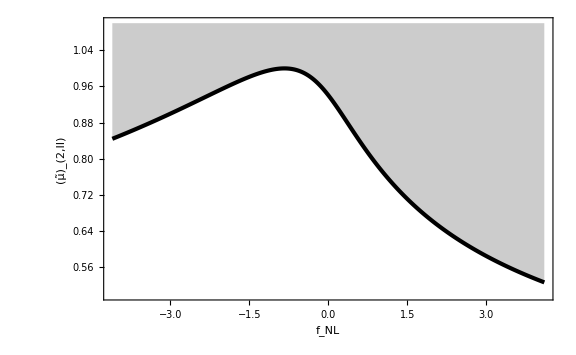

```mathematica
ListPlot[mu2List,PlotStyle->{AbsoluteThickness[3],Black},Filling->Top,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2,II]},PlotRange->{0.5,1.1}]
```

```mathematica
mu2int[fNL_]=Interpolation[mu2List][fNL];
```

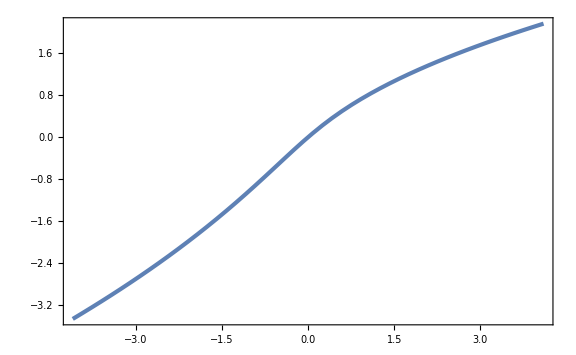

```mathematica
Plot[mu2int[fNL]fNL,{fNL,-4.1,4.1},GridLines->{None,{-5/6}}]
```

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3.7}]},{mufNL,-5,5,10^-2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

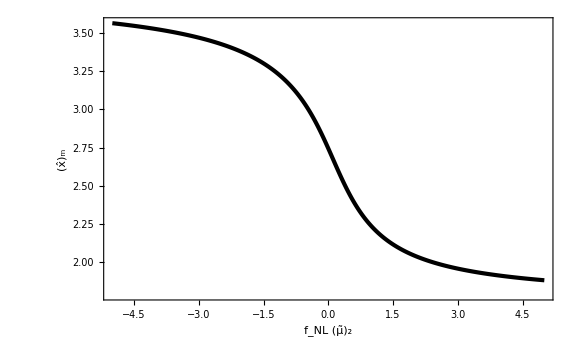

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Cpp[x_,mu_,fNL_]=D[D[CompactC[x,mu,fNL], x], x]//Simplify
```

1/(75 x^6)4 (-10 (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x]))^2+8 x (5 x^2+mu (x Cos[x]-Sin[x]) (5 x+6 fNL mu Sin[x])) (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))-x^2 (10 x+mu (5+6 fNL mu Cos[x]) (x Cos[x]-Sin[x])-mu x Sin[x] (5 x+6 fNL mu Sin[x]))^2+x^2 (5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])) (mu x Cos[x] (5 x+24 fNL mu Sin[x])+5 (-2+3 mu x Sin[x])))

```mathematica
qq[mu_,fNL_]=-(xmint[mu fNL]^2 Cpp[xmint[mu fNL],mu,fNL])/(4(1-3/2 CompactC[xmint[mu fNL],mu,fNL])CompactC[xmint[mu fNL],mu,fNL]);
```

```mathematica
Cq[x_,mu_,fNL_]=(CompactC[xmint[mu fNL],mu,fNL] x^2)/(xmint[mu fNL]^2 E^(2zetabar[xmint[mu fNL],mu,fNL]))Exp[1/qq[mu,fNL](1-(x/(xmint[mu fNL] E^zetabar[xmint[mu fNL],mu,fNL]))^(2qq[mu,fNL]))];
```

```mathematica
Cbarmq[mu_,fNL_]:=3/2 E^(1/qq[mu,fNL])qq[mu,fNL]^(-1+5/(2qq[mu,fNL]))(Gamma[5/(2qq[mu,fNL])]-Gamma[5/(2qq[mu,fNL]),1/qq[mu,fNL]])CompactC[xmint[mu fNL],mu,fNL]/;mu<mu2int[fNL]
Cbarmq[mu_,fNL_]:=None/;!(mu<mu2int[fNL])
```

```mathematica
CbarmqmaxData=ParallelTable[{fNL,FindMaximum[{Cbarmq[mu,fNL],10^-2≤mu≤mu2int[fNL]},{mu,1/4}]},{fNL,-4,4,1/100}];//AbsoluteTiming
```

{16.1734,Null}

```mathematica
CbarmqmaxList=Table[{CbarmqmaxData[[i,1]],CbarmqmaxData[[i,2,1]]},{i,Length[CbarmqmaxData]}];
muqmaxList=Table[{CbarmqmaxData[[i,1]],mu/.CbarmqmaxData[[i,2,2]]},{i,Length[CbarmqmaxData]}];
```

```mathematica
Export["Cbarmqmax.dat",CbarmqmaxList];
Export["muqmax.dat",muqmaxList];
```

```mathematica
CbarmqmaxList=Import["Cbarmqmax.dat"]//ToExpression;
muqmaxList=Import["muqmax.dat"]//ToExpression;
```

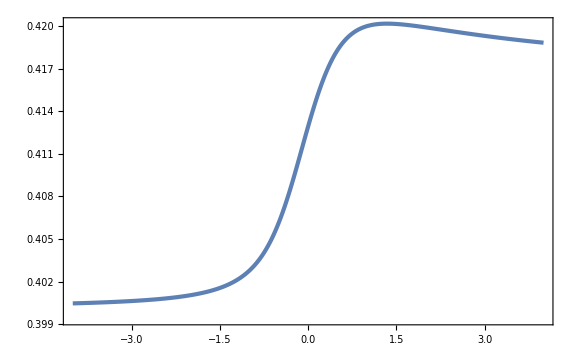

```mathematica
ListPlot[CbarmqmaxList]
```

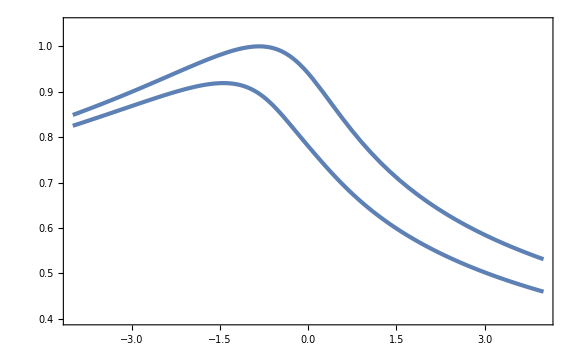

```mathematica
Show[ListPlot[muqmaxList,PlotRange->{0.4,1.05}],Plot[mu2int[fNL],{fNL,-4,4}]]
```

```mathematica
Cbarqmaxint[fNL_]=Interpolation[CbarmqmaxList][fNL];
```

```mathematica
Cbarqth=Cbarqmaxint[-125/100]
```

0.402021

```mathematica
muthqList=Table[{fNL,mu/.FindRoot[Cbarmq[mu,fNL]==2/5,{mu,1/4}]},{fNL,-4,4,1/100}];//AbsoluteTiming
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{10.9821,Null}

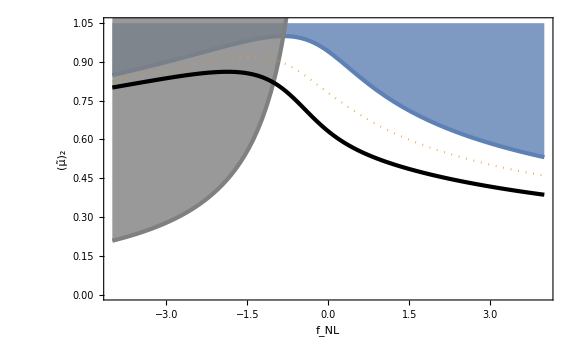

```mathematica
Show[Plot[mu2int[fNL],{fNL,-4,4},Filling->Top,FillingStyle->Opacity[0.8],PlotRange->{0,1.05},FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2]}],Plot[-5/(6fNL),{fNL,-4,0},PlotStyle->{Gray,AbsoluteThickness[3]},Filling->Top,FillingStyle->Opacity[0.8]],ListPlot[{muthqList,muqmaxList},PlotStyle->{{Black,AbsoluteThickness[3]},Dotted}]]
```

```mathematica
muthqint[fNL_]=Interpolation[muthqList][fNL];
```

```mathematica
alpha[mu_,fNL_]=KK(mu-muthqint[fNL])^γ/.{KK->1,γ->0.36};
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]alpha[mu,fNL];
dLogMdmu[mu_,fNL_]=D[Log[MoMks[mu,fNL]], mu]//Simplify;
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu,fNL]]^-1 UnitStep[mu-muthqint[fNL]];
```

```mathematica
fPBHListfNLm1=Flatten[ParallelTable[{MoMks[muthqint[-1]+10^logmu,-1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[-1]+10^logmu,-1]//Quiet},{logmu,-10,Log10[mu2int[-1]-muthqint[-1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL0=Flatten[ParallelTable[{MoMks[muthqint[0]+10^logmu,0],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[0]+10^logmu,0]//Quiet},{logmu,-10,Log10[mu2int[0]-muthqint[0]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL1=Flatten[ParallelTable[{MoMks[muthqint[1]+10^logmu,1],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[1]+10^logmu,1]//Quiet},{logmu,-10,Log10[mu2int[1]-muthqint[1]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL2=Flatten[ParallelTable[{MoMks[muthqint[2]+10^logmu,2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[2]+10^logmu,2]//Quiet},{logmu,-10,Log10[mu2int[2]-muthqint[2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL3=Flatten[ParallelTable[{MoMks[muthqint[3]+10^logmu,3],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[3]+10^logmu,3]//Quiet},{logmu,-10,Log10[mu2int[3]-muthqint[3]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL4=Flatten[ParallelTable[{MoMks[muthqint[4]+10^logmu,4],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[4]+10^logmu,4]//Quiet},{logmu,-10,Log10[mu2int[4]-muthqint[4]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHListfNL52=Flatten[ParallelTable[{MoMks[muthqint[5/2]+10^logmu,5/2],10^logA,fPBH[10^20,1.56 10^13,10^logA,muthqint[5/2]+10^logmu,5/2]//Quiet},{logmu,-10,Log10[mu2int[5/2]-muthqint[5/2]],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{14.4359,Null}

{14.3077,Null}

{14.2076,Null}

{14.2361,Null}

{14.4039,Null}

```mathematica
Export["fPBHqfNLm1.dat",fPBHListfNLm1];
Export["fPBHqfNL0.dat",fPBHListfNL0];
Export["fPBHqfNL1.dat",fPBHListfNL1];
Export["fPBHqfNL2.dat",fPBHListfNL2];
Export["fPBHqfNL3.dat",fPBHListfNL3];
Export["fPBHqfNL4.dat",fPBHListfNL4];
Export["fPBHqfNL52.dat",fPBHListfNL52];
```

```mathematica
fPBHListfNLm1=Import["fPBHqfNLm1.dat"]//ToExpression;
fPBHListfNL0=Import["fPBHqfNL0.dat"]//ToExpression;
fPBHListfNL1=Import["fPBHqfNL1.dat"]//ToExpression;
fPBHListfNL2=Import["fPBHqfNL2.dat"]//ToExpression;
fPBHListfNL3=Import["fPBHqfNL3.dat"]//ToExpression;
fPBHListfNL4=Import["fPBHqfNL4.dat"]//ToExpression;
fPBHListfNL52=Import["fPBHqfNL52.dat"]//ToExpression;
```

```mathematica
fPBHintfNLm1[M_,A_]=Interpolation[fPBHListfNLm1][M,A]UnitStep[MoMks[mu2int[-1],-1]-M,M-MoMks[muthqint[-1]+10^-10,-1]];
fPBHintfNL0[M_,A_]=Interpolation[fPBHListfNL0][M,A]UnitStep[MoMks[mu2int[0],0]-M,M-MoMks[muthqint[0]+10^-10,0]];
fPBHintfNL1[M_,A_]=Interpolation[fPBHListfNL1][M,A]UnitStep[MoMks[mu2int[1],1]-M,M-MoMks[muthqint[1]+10^-10,1]];
fPBHintfNL2[M_,A_]=Interpolation[fPBHListfNL2][M,A]UnitStep[MoMks[mu2int[2],2]-M,M-MoMks[muthqint[2]+10^-10,2]];
fPBHintfNL3[M_,A_]=Interpolation[fPBHListfNL3][M,A]UnitStep[MoMks[mu2int[3],3]-M,M-MoMks[muthqint[3]+10^-10,3]];
fPBHintfNL4[M_,A_]=Interpolation[fPBHListfNL4][M,A]UnitStep[MoMks[mu2int[4],4]-M,M-MoMks[muthqint[4]+10^-10,4]];
fPBHintfNL52[M_,A_]=Interpolation[fPBHListfNL52][M,A]UnitStep[MoMks[mu2int[5/2],5/2]-M,M-MoMks[muthqint[5/2]+10^-10,5/2]];
```

```mathematica
fPBHAListfNLm1=ParallelTable[{10^logA,NIntegrate[fPBHintfNLm1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHintfNL0[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL1=ParallelTable[{10^logA,NIntegrate[fPBHintfNL1[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-3,0,10^-2}];//AbsoluteTiming
fPBHAListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHintfNL2[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL3=ParallelTable[{10^logA,NIntegrate[fPBHintfNL3[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHintfNL4[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
fPBHAListfNL52=ParallelTable[{10^logA,NIntegrate[fPBHintfNL52[E^logM,10^logA],{logM,Log[10^-2],Log[10]}]},{logA,-7/2,0,10^-2}];//AbsoluteTiming
```

{3.93646,Null}

```mathematica
Export["fPBHAqfNLm1.dat",fPBHAListfNLm1];
Export["fPBHAqfNL0.dat",fPBHAListfNL0];
Export["fPBHAqfNL1.dat",fPBHAListfNL1];
Export["fPBHAqfNL2.dat",fPBHAListfNL2];
Export["fPBHAqfNL3.dat",fPBHAListfNL3];
Export["fPBHAqfNL4.dat",fPBHAListfNL4];
Export["fPBHAqfNL52.dat",fPBHAListfNL52];
```

```mathematica
fPBHAListfNLm1=Import["fPBHAqfNLm1.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAqfNL0.dat"]//ToExpression;
fPBHAListfNL1=Import["fPBHAqfNL1.dat"]//ToExpression;
fPBHAListfNL2=Import["fPBHAqfNL2.dat"]//ToExpression;
fPBHAListfNL3=Import["fPBHAqfNL3.dat"]//ToExpression;
fPBHAListfNL4=Import["fPBHAqfNL4.dat"]//ToExpression;
fPBHAListfNL52=Import["fPBHAqfNL52.dat"]//ToExpression;
```

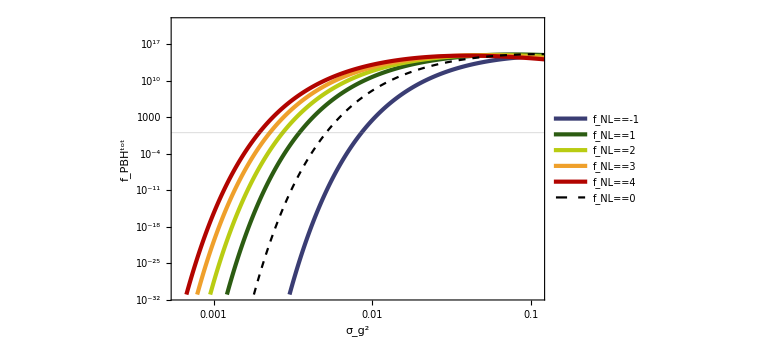

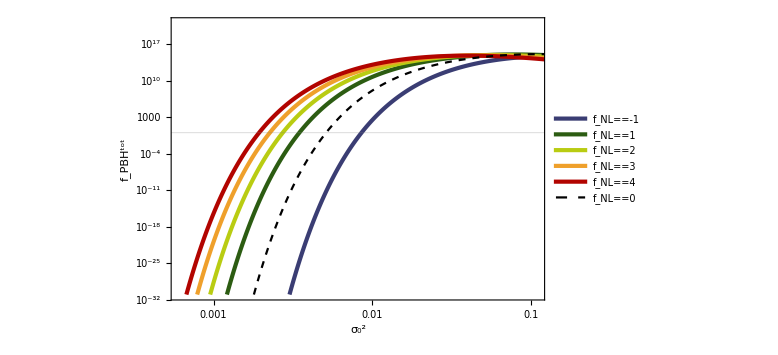

```mathematica
FigfPBHtotfNL=ListLogLogPlot[{fPBHAListfNLm1,fPBHAListfNL1,fPBHAListfNL2,fPBHAListfNL3,fPBHAListfNL4,fPBHAListfNL0},FrameLabel->{Subscript[σ, 0]^2,Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==-1,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.7,0.2}]]
```

```mathematica
Export["fPBHtotfNL.pdf",FigfPBHtotfNL];
```

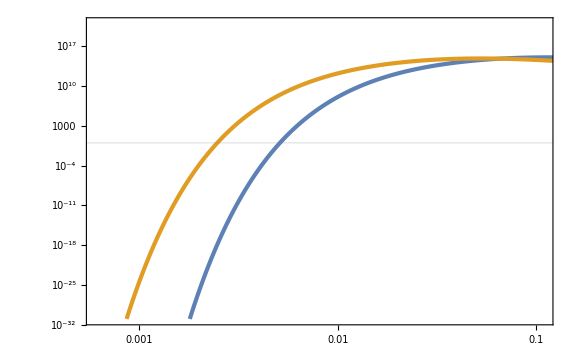

```mathematica
ListLogLogPlot[{fPBHAListfNL0,fPBHAListfNL52},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}}]
```

```mathematica
fPBHAintfNLm1[A_]=Interpolation[fPBHAListfNLm1][A];
fPBHAintfNL0[A_]=Interpolation[fPBHAListfNL0][A];
fPBHAintfNL1[A_]=Interpolation[fPBHAListfNL1][A];
fPBHAintfNL2[A_]=Interpolation[fPBHAListfNL2][A];
fPBHAintfNL3[A_]=Interpolation[fPBHAListfNL3][A];
fPBHAintfNL4[A_]=Interpolation[fPBHAListfNL4][A];
fPBHAintfNL52[A_]=Interpolation[fPBHAListfNL52][A];
```

```mathematica
A1fNLm1=A/.FindRoot[Log10[fPBHAintfNLm1[A]]==0,{A,0.005}]
A1fNL0=A/.FindRoot[Log10[fPBHAintfNL0[A]]==0,{A,0.005}]
A1fNL1=A/.FindRoot[Log10[fPBHAintfNL1[A]]==0,{A,0.003}]
A1fNL2=A/.FindRoot[Log10[fPBHAintfNL2[A]]==0,{A,0.003}]
A1fNL3=A/.FindRoot[Log10[fPBHAintfNL3[A]]==0,{A,0.003}]
A1fNL4=A/.FindRoot[Log10[fPBHAintfNL4[A]]==0,{A,0.003}]
A1fNL52=A/.FindRoot[Log10[fPBHAintfNL52[A]]==0,{A,0.003}]
```

0.0085586

0.00511925

0.00347123

0.00272836

0.00226253

0.00193664

0.00247261

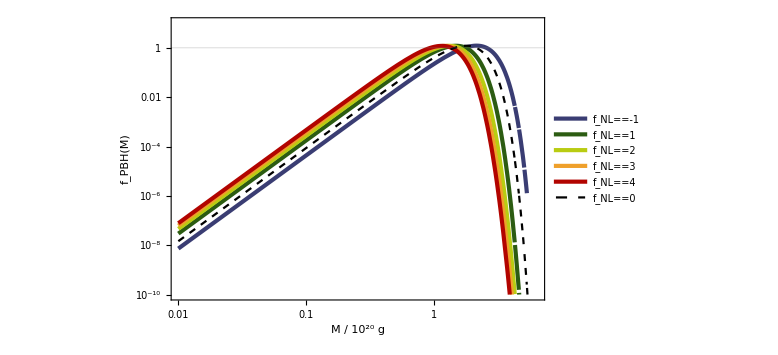

```mathematica
FigfPBHfNL=LogLogPlot[{fPBHintfNLm1[M,A1fNLm1],fPBHintfNL1[M,A1fNL1],fPBHintfNL2[M,A1fNL2],fPBHintfNL3[M,A1fNL3],fPBHintfNL4[M,A1fNL4],fPBHintfNL0[M,A1fNL0]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / 10^20 g"}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[7]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[3]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{Black,Dashed}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==-1,Subscript[f, NL]==1,Subscript[f, NL]==2,Subscript[f, NL]==3,Subscript[f, NL]==4,Subscript[f, NL]==0},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendLayout->{"Column",2},LegendMarkerSize->20],{0.6,0.2}]]
```

```mathematica
Export["fPBHfNL.pdf",FigfPBHfNL];
```

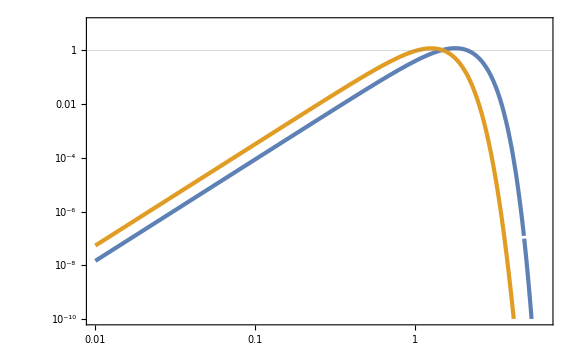

```mathematica
LogLogPlot[{fPBHintfNL0[M,A1fNL0],fPBHintfNL52[M,A1fNL52]},{M,0.01,10},GridLines->{None,{1}},PlotRange->{10^-10,10}]
```

```mathematica
Export["fPBHintfNL0.wdx",fPBHintfNL0[M,A1fNL0]];
Export["fPBHintfNL52.wdx",fPBHintfNL52[M,A1fNL52]];
```

#### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

1.41746 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

(0.281448 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A)

(0.281448 ⅇ^(-(0.248855 dl^2)/A))/(√A)

General::munfl: Exp[-10658.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

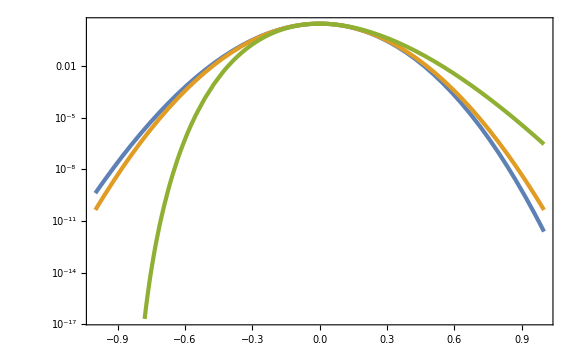

```mathematica
LogPlot[{PfNL[dl,10^-2,fNLmin],PGauss[dl,10^-2],PfNL[dl,10^-2,2]},{dl,-1,1}]
```

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->0.587}

βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A (1-(3 dl)/4))

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(0.248855 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

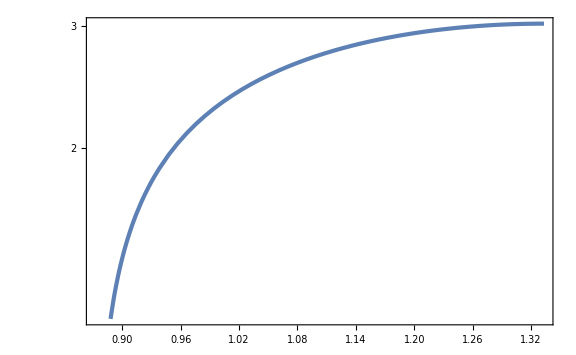

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

```mathematica
fPBHPSListfNLmin=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,fNLmin]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL2=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL4=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,4]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.4048,Null}

{4.99572,Null}

{7.26934,Null}

{6.84714,Null}

```mathematica
Export["fPBHPSfNLmin.dat",fPBHPSListfNLmin];
Export["fPBHPSfNL0.dat",fPBHPSListfNL0];
Export["fPBHPSfNL2.dat",fPBHPSListfNL2];
Export["fPBHPSfNL4.dat",fPBHPSListfNL4];
```

```mathematica
fPBHPSListfNLmin=Import["fPBHPSfNLmin.dat"]//ToExpression;
fPBHPSListfNL0=Import["fPBHPSfNL0.dat"]//ToExpression;
fPBHPSListfNL2=Import["fPBHPSfNL2.dat"]//ToExpression;
fPBHPSListfNL4=Import["fPBHPSfNL4.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSintfNLmin[M_,A_]=Interpolation[fPBHPSListfNLmin][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL2[M_,A_]=Interpolation[fPBHPSListfNL2][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL4[M_,A_]=Interpolation[fPBHPSListfNL4][M,A]UnitStep[Mmax-M,M-Mmin];
```

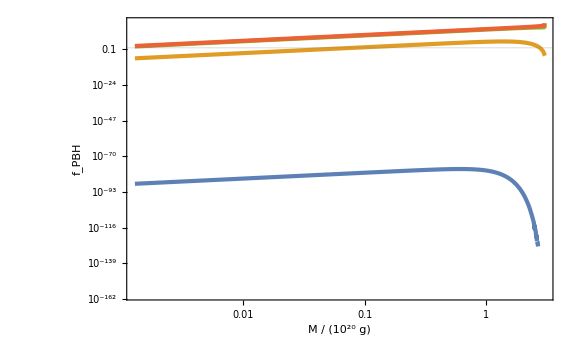

```mathematica
LogLogPlot[{fPBHPSintfNLmin[M,10^-3],fPBHPSintfNLmin[M,10^-2],fPBHPSintfNLmin[M,10^-1],fPBHPSintfNLmin[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

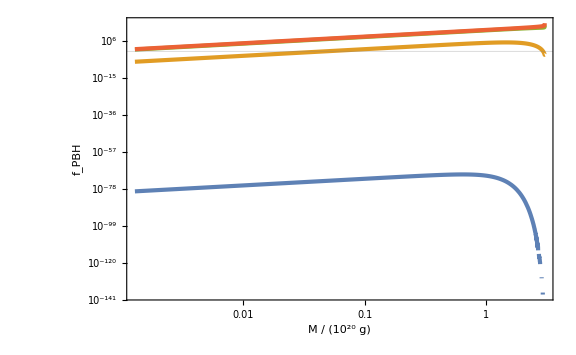

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

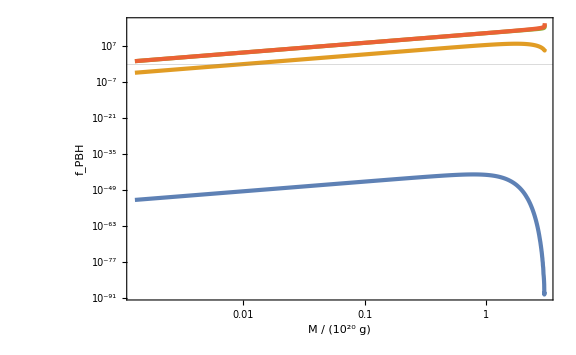

```mathematica
LogLogPlot[{fPBHPSintfNL2[M,10^-3],fPBHPSintfNL2[M,10^-2],fPBHPSintfNL2[M,10^-1],fPBHPSintfNL2[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

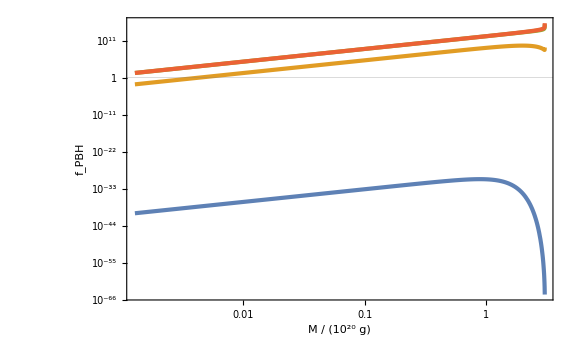

```mathematica
LogLogPlot[{fPBHPSintfNL4[M,10^-3],fPBHPSintfNL4[M,10^-2],fPBHPSintfNL4[M,10^-1],fPBHPSintfNL4[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

```mathematica
fPBHAPSListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNLmin[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL2[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL4[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.9394,Null}

{9.95662,Null}

{9.94781,Null}

{10.1006,Null}

```mathematica
Export["fPBHAPSfNLmin.dat",fPBHAPSListfNLmin];
Export["fPBHAPSfNL0.dat",fPBHAPSListfNL0];
Export["fPBHAPSfNL2.dat",fPBHAPSListfNL2];
Export["fPBHAPSfNL4.dat",fPBHAPSListfNL4];
```

```mathematica
fPBHAPSListfNLmin=Import["fPBHAPSfNLmin.dat"]//ToExpression;
fPBHAPSListfNL0=Import["fPBHAPSfNL0.dat"]//ToExpression;
fPBHAPSListfNL2=Import["fPBHAPSfNL2.dat"]//ToExpression;
fPBHAPSListfNL4=Import["fPBHAPSfNL4.dat"]//ToExpression;
```

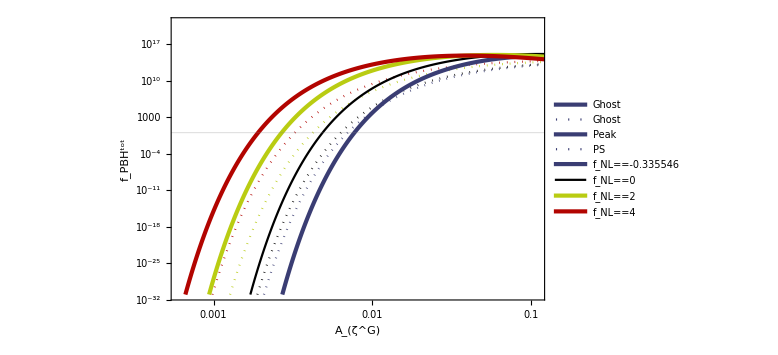

```mathematica
Show[ListLogLogPlot[{fPBHAPSListfNLmin,fPBHAPSListfNL0,fPBHAPSListfNL2,fPBHAPSListfNL4,fPBHAListfNLmin,fPBHAListfNL0,fPBHAListfNL2,fPBHAListfNL4},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Peak","PS",Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.75,0.25}]]]
```

```mathematica
fPBHAPSintfNLmin[A_]=Interpolation[fPBHAPSListfNLmin][A];
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL2[A_]=Interpolation[fPBHAPSListfNL2][A];
fPBHAPSintfNL4[A_]=Interpolation[fPBHAPSListfNL4][A];
```

```mathematica
A1PSfNLmin=A/.FindRoot[Log10[fPBHAPSintfNLmin[A]]==0,{A,0.003}]
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.003}]
A1PSfNL2=A/.FindRoot[Log10[fPBHAPSintfNL2[A]]==0,{A,0.003}]
A1PSfNL4=A/.FindRoot[Log10[fPBHAPSintfNL4[A]]==0,{A,0.003}]
```

0.00699411

0.00633633

0.00422324

0.00325043

InterpolatingFunction::dmval: Input value {0.000100024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

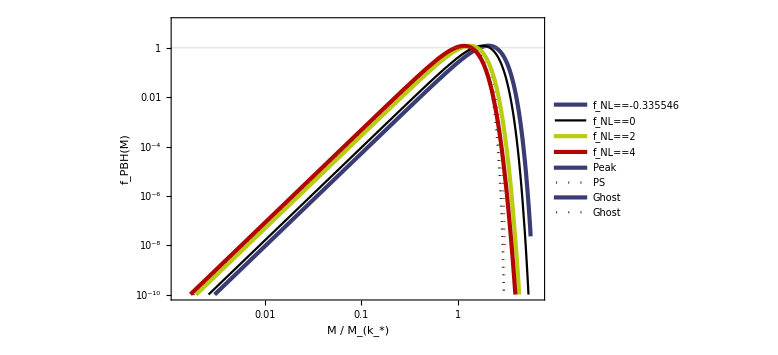

```mathematica
Show[LogLogPlot[{fPBHPSintfNLmin[M,A1PSfNLmin],fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL2[M,A1PSfNL2],fPBHPSintfNL4[M,A1PSfNL4],fPBHintfNLmin[M,A1fNLmin],fPBHintfNL0[M,A1fNL0],fPBHintfNL2[M,A1fNL2],fPBHintfNL4[M,A1fNL4]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4,"Peak","PS","Ghost","Ghost"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.3,0.65}]]]
```

### exp

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_]=-1/3 Log[1-3zetaGx[x,mu]]//Simplify
```

-1/3 Log[1-(3 mu Sin[x])/x]

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//FullSimplify
```

-(2 mu (x Cos[x]-Sin[x]) (2 x+mu x Cos[x]-7 mu Sin[x]))/(3 (x-3 mu Sin[x])^2)

```mathematica
rmcond[x_,mu_]=-1/(mu x^2)(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

(-3 mu x+(-1+x^2) Sin[x]+Cos[x] (x+3 mu Sin[x]))/(x^2 (x-3 mu Sin[x])^2)

```mathematica
rmcond2[x_,mu_]=(1+x D[zetabar[x,mu], x])//Simplify
```

(x+mu x Cos[x]-4 mu Sin[x])/(x-3 mu Sin[x])

```mathematica
xmList=Sort[Table[{1/3-10^logmu,x/.FindRoot[rmcond[x,1/3-10^logmu]==0,{x,0.1}]},{logmu,-6,Log10[1/3],10^-2}],#1[[1]]<#2[[1]]&];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

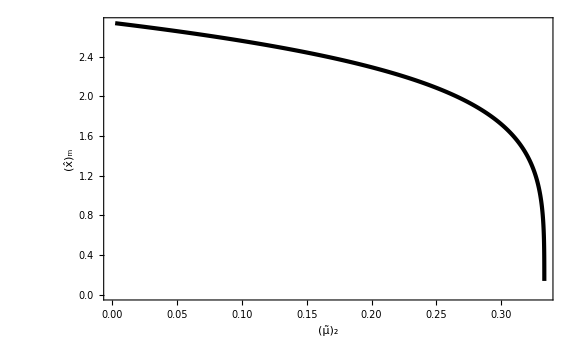

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2],Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black},PlotRange->Full]
```

```mathematica
xmint[mu_]=Interpolation[xmList][mu];
```

```mathematica
Cpp[x_,mu_]=D[D[CompactC[x,mu], x], x]//Simplify
```

1/(6 (x-3 mu Sin[x])^4)mu (-36 mu-297 mu^3+48 mu x^2-144 mu^3 x^2+2 (mu^2 (54-33 x^2)+4 x^2 (-2+x^2)) Cos[x]-4 mu (-9-6 x^2-2 x^4+18 mu^2 (-4+x^2)) Cos[2 x]-108 mu^2 Cos[3 x]+66 mu^2 x^2 Cos[3 x]+9 mu^3 Cos[4 x]+16 x Sin[x]+36 mu^2 x Sin[x]-8 x^3 Sin[x]+54 mu^2 x^3 Sin[x]+432 mu^3 x Sin[2 x]-16 mu x^3 Sin[2 x]-156 mu^2 x Sin[3 x]+6 mu^2 x^3 Sin[3 x])

```mathematica
qq[mu_]=-(xmint[mu]^2 Cpp[xmint[mu],mu])/(4(1-3/2 CompactC[xmint[mu],mu])CompactC[xmint[mu],mu]);
```

```mathematica
Cq[x_,mu_]=(CompactC[xmint[mu],mu] x^2)/(xmint[mu]^2 E^(2zetabar[xmint[mu],mu]))Exp[1/qq[mu](1-(x/(xmint[mu] E^zetabar[xmint[mu],mu]))^(2qq[mu]))];
```

```mathematica
Cbarmq[mu_]:=3/2 E^(1/qq[mu])qq[mu]^(-1+5/(2qq[mu]))(Gamma[5/(2qq[mu])]-Gamma[5/(2qq[mu]),1/qq[mu]])CompactC[xmint[mu],mu]/;mu<1/3
Cbarmq[mu_]:=None/;!(mu<1/3)
```

```mathematica
muth=mu/.FindRoot[Cbarmq[mu]==2/5,{mu,0.3},WorkingPrecision->30]
```

0.305522661838031813238284641757

```mathematica
alpha[mu_]=KK(mu-muth)^γ/.{KK->1,γ->36/100};
```

```mathematica
MoMks[mu_]=xmint[mu]^2 Exp[2zetabar[xmint[mu],mu]]alpha[mu];
dLogMdmu[mu_]=D[Log[MoMks[mu]], mu]//Simplify;
```

```mathematica
mumax=mu/.FindMaximum[{MoMks[mu],muth<mu<1/3},{mu,0.33},WorkingPrecision->30][[2]]
Mmax=MoMks[mumax]
```

FindMaximum::precw: The precision of the argument function (-((-0.305522661838032+mu)^(9/25) («1»)^2)/(1-(3 mu Sin[InterpolatingFunction[«1»][mu]])/(InterpolatingFunction[{«1»},«3»,{«1»}][mu]))^(2/3)) is less than WorkingPrecision (30.).

FindMaximum::precw: The precision of the argument function ({{0.3055226618380318<mu,mu<1/3}}) is less than WorkingPrecision (30.).

0.324873740502738483915123879342

0.937548

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
keq=0.07 0.143
```

0.01001

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_]=Mks/10^20 MoMks[mu](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)Abs[dLogMdmu[mu]]^-1 UnitStep[mu-muth];
```

```mathematica
fPBHlowList=Flatten[ParallelTable[{MoMks[muth+10^logmu],10^logA,fPBH[10^20,1.56 10^13,10^logA,muth+10^logmu]//Quiet},{logmu,-10,Log10[mumax-muth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{15.0775,Null}

```mathematica
Export["fPBHexplow.dat",fPBHlowList];
```

```mathematica
fPBHlowList=Import["fPBHexplow.dat"]//ToExpression;
```

```mathematica
fPBHintlow[M_,A_]=Interpolation[fPBHlowList][M,A]UnitStep[MoMks[mumax]-M,M-MoMks[muth]];
```

```mathematica
fPBHAList=ParallelTable[{10^logA,NIntegrate[fPBHintlow[E^logM,10^logA],{logM,Log[10^-2],0}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{3.75806,Null}

```mathematica
Export["fPBHA_exp.dat",fPBHAList];
```

```mathematica
fPBHAList=Import["fPBHA_exp.dat"]//ToExpression;
fPBHAListfNL0=Import["fPBHAqfNL0.dat"]//ToExpression;
fPBHAListfNL52=Import["fPBHAqfNL52.dat"]//ToExpression;
```

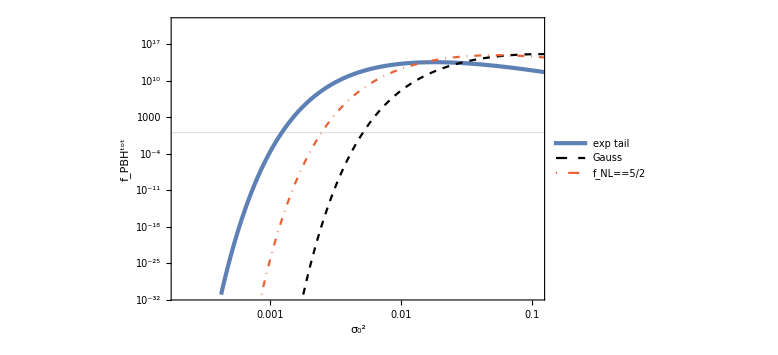

```mathematica
ListLogLogPlot[{fPBHAList,fPBHAListfNL0,fPBHAListfNL52},FrameLabel->{Subscript[σ, 0]^2,Subscript[f, PBH]^tot},PlotRange->{{2 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{AbsoluteThickness[3],{Black,Dashed},{Color[4],DotDashed}},PlotLegends->Placed[LineLegend[{"exp tail","Gauss",Subscript[f, NL]==5/2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20],{0.8,0.3}]]
```

```mathematica
fPBHAint[A_]=Interpolation[fPBHAList][A];
```

```mathematica
A1=A/.FindRoot[Log10[fPBHAint[A]]==0,{A,0.001}]
```

0.00122933

```mathematica
fPBHintfNL0[M_]=Import["fPBHintfNL0.wdx"];
fPBHintfNL52[M_]=Import["fPBHintfNL52.wdx"];
```

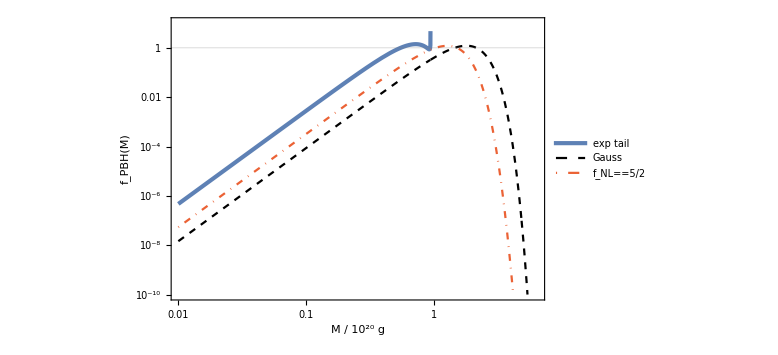

```mathematica
LogLogPlot[{fPBHintlow[M,A1],fPBHintfNL0[M],fPBHintfNL52[M]},{M,0.01,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / 10^20 g"}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{AbsoluteThickness[3],{Black,Dashed},{Color[4],DotDashed}},PlotLegends->Placed[LineLegend[{"exp tail","Gauss",Subscript[f, NL]==5/2},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20],{0.6,0.3}]]
```

#### Press-Schechter

```mathematica
xm=2.74;
```

```mathematica
WRTH[z_]=3/z^3(Sin[z]-z Cos[z]);
```

```mathematica
sX[A_]=4/9 xm^2 WRTH[xm]Sqrt[A]
sY[A_,fNL_]=6/4 fNL Sinc[xm]Sqrt[A]
```

1.41746 √A

0.213988 √A fNL

```mathematica
PfNL[dl_,A_,fNL_]=1/Sqrt[2π sX[A]^2](Exp[(-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)]+Exp[(-((-sX[A]-Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2)/(2 sX[A]^2)])//Simplify
PGauss[dl_,A_]=1/Sqrt[2π sX[A]^2] Exp[Normal[Series[-((-sX[A]+Sqrt[sX[A]^2+4sX[A]sY[A,fNL]dl])/(2sY[A,fNL]))^2,{fNL,0,0}]]/(2 sX[A]^2)]//Simplify
```

(0.281448 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A)

(0.281448 ⅇ^(-(0.248855 dl^2)/A))/(√A)

```mathematica
LogPlot[{PfNL[dl,10^-2,fNLmin],PGauss[dl,10^-2],PfNL[dl,10^-2,2]},{dl,-1,1}]
```

General::munfl: Exp[-10658.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
MoMksPS[dl_]=xm^2 KK(dl-3/8 dl^2-Cth)^γ/.{KK->1,γ->0.36,Cth->0.587}
β[dl_,A_,fNL_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PfNL[dl,A,fNL]/.{KK->1,γ->0.36,Cth->0.587}

βGauss[dl_,A_]=(KK(dl-3/8 dl^2-Cth)^(γ+1))/(γ(1-3/4 dl))PGauss[dl,A]/.{KK->1,γ->0.36,Cth->0.587}
fPBHPS[dl_,A_,fNL_]=β[dl,A,fNL]/(6.88 10^-16);
fPBHPSGauss[dl_,A_]=βGauss[dl,A]/(6.88 10^-16);
```

7.5076 (-0.587+dl-(3 dl^2)/8)^0.36

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 (ⅇ^(-(1.35865 (-1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))+ⅇ^(-(1.35865 (1.41746 √A+√(A (2.00921+1.21328 dl fNL)))^2)/(A^2 fNL^2))))/(√A (1-(3 dl)/4))

(0.7818 (-0.587+dl-(3 dl^2)/8)^1.36 ⅇ^(-(0.248855 dl^2)/A))/(√A (1-(3 dl)/4))

```mathematica
dlth=4/3(1-Sqrt[1-3/2 Cth])/.{Cth->0.587}
dlmax=4/3;
```

0.872416

```mathematica
LogPlot[MoMksPS[dl],{dl,dlth,dlmax}]
```

-Graphics-

```mathematica
fPBHPSListfNLmin=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,fNLmin]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL0=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPSGauss[dlth+10^logdl,10^logA]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL2=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,2]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
fPBHPSListfNL4=Flatten[ParallelTable[{MoMksPS[dlth+10^logdl],10^logA,fPBHPS[dlth+10^logdl,10^logA,4]//Quiet},{logdl,-10,Log10[dlmax-dlth],10^-2},{logA,-4,0,10^-2}],1];//AbsoluteTiming
```

{7.4048,Null}

{4.99572,Null}

{7.26934,Null}

{6.84714,Null}

```mathematica
Export["fPBHPSfNLmin.dat",fPBHPSListfNLmin];
Export["fPBHPSfNL0.dat",fPBHPSListfNL0];
Export["fPBHPSfNL2.dat",fPBHPSListfNL2];
Export["fPBHPSfNL4.dat",fPBHPSListfNL4];
```

```mathematica
fPBHPSListfNLmin=Import["fPBHPSfNLmin.dat"]//ToExpression;
fPBHPSListfNL0=Import["fPBHPSfNL0.dat"]//ToExpression;
fPBHPSListfNL2=Import["fPBHPSfNL2.dat"]//ToExpression;
fPBHPSListfNL4=Import["fPBHPSfNL4.dat"]//ToExpression;
```

```mathematica
Mmax=MoMksPS[dlmax]
Mmin=MoMksPS[dlth+10^-10]
```

3.01968

0.00128655

```mathematica
fPBHPSintfNLmin[M_,A_]=Interpolation[fPBHPSListfNLmin][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL0[M_,A_]=Interpolation[fPBHPSListfNL0][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL2[M_,A_]=Interpolation[fPBHPSListfNL2][M,A]UnitStep[Mmax-M,M-Mmin];
fPBHPSintfNL4[M_,A_]=Interpolation[fPBHPSListfNL4][M,A]UnitStep[Mmax-M,M-Mmin];
```

```mathematica
LogLogPlot[{fPBHPSintfNLmin[M,10^-3],fPBHPSintfNLmin[M,10^-2],fPBHPSintfNLmin[M,10^-1],fPBHPSintfNLmin[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL0[M,10^-3],fPBHPSintfNL0[M,10^-2],fPBHPSintfNL0[M,10^-1],fPBHPSintfNL0[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL2[M,10^-3],fPBHPSintfNL2[M,10^-2],fPBHPSintfNL2[M,10^-1],fPBHPSintfNL2[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
LogLogPlot[{fPBHPSintfNL4[M,10^-3],fPBHPSintfNL4[M,10^-2],fPBHPSintfNL4[M,10^-1],fPBHPSintfNL4[M,1]},{M,Mmin,Mmax},GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotRange->Full]
```

-Graphics-

```mathematica
fPBHAPSListfNLmin=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNLmin[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL0=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL0[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL2=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL2[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
fPBHAPSListfNL4=ParallelTable[{10^logA,NIntegrate[fPBHPSintfNL4[E^logM,10^logA],{logM,Log[Mmin],Log[Mmax]}]//Quiet},{logA,-4,0,10^-2}];//AbsoluteTiming
```

{9.9394,Null}

{9.95662,Null}

{9.94781,Null}

{10.1006,Null}

```mathematica
Export["fPBHAPSfNLmin.dat",fPBHAPSListfNLmin];
Export["fPBHAPSfNL0.dat",fPBHAPSListfNL0];
Export["fPBHAPSfNL2.dat",fPBHAPSListfNL2];
Export["fPBHAPSfNL4.dat",fPBHAPSListfNL4];
```

```mathematica
fPBHAPSListfNLmin=Import["fPBHAPSfNLmin.dat"]//ToExpression;
fPBHAPSListfNL0=Import["fPBHAPSfNL0.dat"]//ToExpression;
fPBHAPSListfNL2=Import["fPBHAPSfNL2.dat"]//ToExpression;
fPBHAPSListfNL4=Import["fPBHAPSfNL4.dat"]//ToExpression;
```

```mathematica
Show[ListLogLogPlot[{fPBHAPSListfNLmin,fPBHAPSListfNL0,fPBHAPSListfNL2,fPBHAPSListfNL4,fPBHAListfNLmin,fPBHAListfNL0,fPBHAListfNL2,fPBHAListfNL4},FrameLabel->{Subscript[A, ζ^("G")],Subscript[f, PBH]^tot},PlotRange->{{6 10^-4,1.1 10^-1},{10^-31,10^21}},GridLines->{None,{1}},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}},PlotLegends->Placed[LineLegend[{"Ghost","Ghost","Peak","PS",Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.75,0.25}]]]
```

-Graphics-

```mathematica
fPBHAPSintfNLmin[A_]=Interpolation[fPBHAPSListfNLmin][A];
fPBHAPSintfNL0[A_]=Interpolation[fPBHAPSListfNL0][A];
fPBHAPSintfNL2[A_]=Interpolation[fPBHAPSListfNL2][A];
fPBHAPSintfNL4[A_]=Interpolation[fPBHAPSListfNL4][A];
```

```mathematica
A1PSfNLmin=A/.FindRoot[Log10[fPBHAPSintfNLmin[A]]==0,{A,0.003}]
A1PSfNL0=A/.FindRoot[Log10[fPBHAPSintfNL0[A]]==0,{A,0.003}]
A1PSfNL2=A/.FindRoot[Log10[fPBHAPSintfNL2[A]]==0,{A,0.003}]
A1PSfNL4=A/.FindRoot[Log10[fPBHAPSintfNL4[A]]==0,{A,0.003}]
```

0.00699411

0.00633633

0.00422324

0.00325043

```mathematica
Show[LogLogPlot[{fPBHPSintfNLmin[M,A1PSfNLmin],fPBHPSintfNL0[M,A1PSfNL0],fPBHPSintfNL2[M,A1PSfNL2],fPBHPSintfNL4[M,A1PSfNL4],fPBHintfNLmin[M,A1fNLmin],fPBHintfNL0[M,A1fNL0],fPBHintfNL2[M,A1fNL2],fPBHintfNL4[M,A1fNL4]},{M,10^-4,10},GridLines->{None,{1}},FrameLabel->{Row[{M," / ",Subscript[M, SubStar[k]]}],Subscript[f, PBH][M]},PlotRange->{10^-10,10},PlotStyle->{{ColorData[10,"ColorList"][[9]],Dotted},{Black,Dotted},{ColorData[10,"ColorList"][[5]],Dotted},{ColorData[10,"ColorList"][[1]],Dotted},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]}}],
LogLogPlot[{0,0,0,0,0,0,0,0},{x,0.1,1},PlotStyle->{{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Black},{AbsoluteThickness[3],ColorData[10,"ColorList"][[5]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[1]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]},{AbsoluteThickness[3],ColorData[10,"ColorList"][[9]]},{Dotted,ColorData[10,"ColorList"][[9]]}},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==fNLmin,Subscript[f, NL]==0,Subscript[f, NL]==2,Subscript[f, NL]==4,"Peak","PS","Ghost","Ghost"},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"],LegendMarkerSize->20,LegendLayout->{"Column",2}],{0.3,0.65}]]]
```

InterpolatingFunction::dmval: Input value {0.000100024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000126515,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.000160024,0.00699411} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

## merger rate

```mathematica
a=(nPBH x^4)/((1+zeq)fPBH);
e=Sqrt[1-(x/y)^6];
```

```mathematica
Solve[{a==aa,e==ee},{x,y}]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(1/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(1/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(1/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(1/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(1/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(1/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(1/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(1/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(2/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(2/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(2/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(ⅈ aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(2/3) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(5/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→-((-1)^(5/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→-(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(5/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))},{x→(aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/nPBH^(1/4),y→((-1)^(5/6) aa^(1/4) fPBH^(1/4) (1+zeq)^(1/4))/((-1+ee^2)^(1/6) nPBH^(1/4))}}

```mathematica
xsol=(aa^(1/4)fPBH^(1/4)(1+zeq)^(1/4))/nPBH^(1/4);
ysol=(aa^(1/4)fPBH^(1/4)(1+zeq)^(1/4))/((1-ee^2)^(1/6)nPBH^(1/4));
```

```mathematica
a/.{x->xsol,y->ysol}
Simplify[e/.{x->xsol,y->ysol},{ee>0}]
```

aa

ee

```mathematica
J=Simplify[Det[{{D[a, x],D[a, y]},{D[e, x],D[e, y]}}]/.{x->xsol,y->ysol},{aa>0,ee>0}]
```

(12 (1-ee^2)^(7/6) √(aa nPBH))/(ee √fPBH √(1+zeq))

```mathematica
dPdade=Simplify[4π xsol^2 nPBH 4π ysol^2 nPBH/J]
```

(4 ee fPBH^(3/2) √(aa nPBH) π^2 (1+zeq)^(3/2))/(3 (1-ee^2)^(3/2))

```mathematica
asol=(t/(Q(1-ee^2)^(7/2)))^(1/4);
```

```mathematica
dPdtde=Simplify[dPdade D[asol, t]/.{aa->asol},Assumptions->{ee^2<1}]
```

(ee fPBH^(3/2) π^2 (nPBH (t/Q)^(1/4))^(3/2) (1+zeq)^(3/2))/(3 (1-ee^2)^(45/16) nPBH t)

```mathematica
dPdt=Simplify[Integrate[dPdtde,{ee,0,eu},Assumptions->{0<eu<1}],{nPBH>0}]
```

(8 (-1+1/((1-eu^2)^(29/16))) fPBH^(3/2) √nPBH π^2 (t/Q)^(3/8) (1+zeq)^(3/2))/(87 t)

```mathematica
Simplify[dPdt/(3/58(t/T)^(3/8)(1/((1-eu^2)^(29/16))-1)1/t),{Q>0,t>0,T>0}]
```

16/9 fPBH^(3/2) √nPBH π^2 (T/Q)^(3/8) (1+zeq)^(3/2)

```mathematica
Solve[ome2==((4π)/3 nPBH)^2(((1+zeq)fPBH)/nPBH(t/(Q ome2^(7/2)))^(1/4))^(3/2)/.{Q->T((3((4π)/3 nPBH)^(-1/3))/(4π fPBH(1+zeq)))^-4},ome2]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{ome2→t^(6/37)/T^(6/37)},{ome2→-((-1)^(1/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(2/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(3/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(4/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(5/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(6/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(7/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(8/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(9/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(10/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(11/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(12/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(13/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(14/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(15/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(16/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(17/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(18/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(19/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(20/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(21/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(22/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(23/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(24/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(25/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(26/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(27/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(28/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(29/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(30/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(31/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(32/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(33/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(34/37) t^(6/37))/T^(6/37)},{ome2→-((-1)^(35/37) t^(6/37))/T^(6/37)},{ome2→((-1)^(36/37) t^(6/37))/T^(6/37)}}

```mathematica
$Assumptions={eV>0};
```

```mathematica
Mpl=(1.22 10^(19+9))/Sqrt[8π] eV;
km=10^3/(1.973 10^-7)eV^-1;
sec=1/(6.582 10^-16)eV^-1;
pc=3.086 10^(16-3)km;
kg=1/(1.783 10^-36)eV;
yr=365.2425 24 60 60sec;
G=1/(8π Mpl^2);
```

```mathematica
Modot=2 10^30 kg;
Ms=30Modot;
ts=14 10^9 yr
```

(6.7122×10^32)/eV

```mathematica
h=0.67;
ODMh2=0.12;
Omh2=0.143;
zeq=2.4 10^4 Omh2
```

3432.

```mathematica
ρc0=3 Mpl^2(h 100 km/(sec 10^6 pc))^2
```

3.62806×10^-11 eV^4

```mathematica
nPBH[fPBH_]=fPBH ODMh2/h^2 ρc0/Ms
```

2.88208×10^-79 eV^3 fPBH

```mathematica
ymax[fPBH_]=((4π)/3 nPBH[fPBH])^(-1/3)//Simplify
```

(9.3915×10^25)/(eV fPBH^(1/3))

```mathematica
T[fPBH_]=3/170 1/(G^3 Ms^3)((3ymax[fPBH])/(4π fPBH(1+zeq)))^4//Simplify
```

(2.77793×10^51)/(eV fPBH^(16/3))

```mathematica
tc[fPBH_]=T[fPBH]((4π fPBH)/3)^(37/3)
```

(1.30662×10^59 fPBH^7)/eV

```mathematica
Clear[eupper]
eupper[fPBH_]:=Sqrt[1-(ts/T[fPBH])^(6/37)]/;Simplify[ts/tc[fPBH]]<1
eupper[fPBH_]:=Sqrt[1-((4π fPBH)/3)^2(ts/tc[fPBH])^(2/7)]/;Simplify[ts/tc[fPBH]]>=1
```

```mathematica
Clear[calR]
calR[fPBH_]:=(3nPBH[fPBH])/58(ts/T[fPBH])^(3/8)(1/((1-eupper[fPBH]^2)^(29/16))-1)1/ts(10^9 pc)^3 yr
```

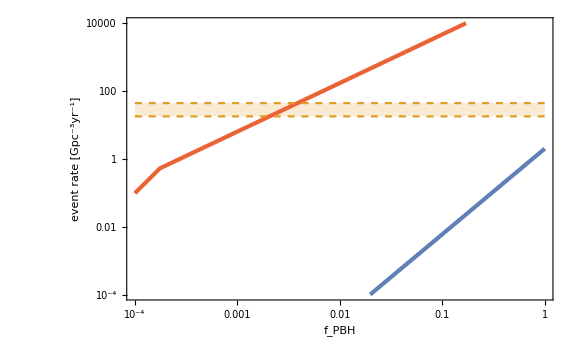

```mathematica
LogLogPlot[{calR[fPBH],2 fPBH^(53/21),44,17.9},{fPBH,10^-4,1},PlotRange->{10^-4,10^4},Filling->{3->{4}},PlotStyle->{{AbsoluteThickness[3],Color[4]},{AbsoluteThickness[3],Color[1]},{Color[2],Dashed},{Color[2],Dashed}},FrameLabel->{Subscript[f, PBH],"event rate [Gpc^-3yr^-1]"}]
```

## curvaton

```mathematica
$Assumptions={pp>0,tp>0,pm>0,tm>0,F2>0};
```

```mathematica
V[pp_,tp_,pm_,tm_]=h^2(pp Exp[I tp]pm Exp[I tm]-F2)Conjugate[pp Exp[I tp]pm Exp[I tm]-F2]//Simplify//Expand//ExpToTrig
```

F2^2 h^2+h^2 pm^2 pp^2-2 F2 h^2 pm pp Cos[tm+tp]

```mathematica
D[V[pp,tp,pm,-tp], pm]//Simplify
```

2 h^2 pp (-F2+pm pp)

```mathematica
D[V[pp,tp,pm,-tp], pp]//Simplify
```

2 h^2 pm (-F2+pm pp)

```mathematica
D[D[V[pp,tp,pm,-tp], pm], pm]//Simplify
D[D[V[pp,tp,pm,-tp], pp], pp]//Simplify
D[D[V[pp,tp,pm,-tp], pp], pm]//Simplify
```

2 h^2 pp^2

2 h^2 pm^2

-2 h^2 (F2-2 pm pp)

```mathematica
Plot3D[Log[(pp pm-1)^2+10^-2(pp^2+pm^2)],{pp,-5,5},{pm,-5,5}]
```

-Graphics3D-

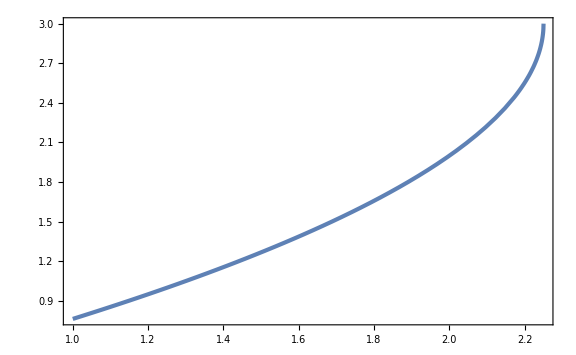

```mathematica
Plot[3-3Sqrt[1-4/9 c],{c,1,9/4}]
```

## power spectrum

```mathematica
CMBLSSlow=Import["CMBLSSlow.csv","Data"].{{1,0},{0,10^-9}};
CMBLSShigh=Import["CMBLSShigh.csv","Data"].{{1,0},{0,10^-9}};
EPTA=Import["EPTA.csv","Data"];
(*LIGOO2=Import["LIGOO2.csv","Data"];*)
LIGOO3=Import["LIGOO3.csv"];
PBHconst=Import["PBHconst.csv","Data"];
```

```mathematica
CMBmu[k_]=(9 10^-5)/(2.2(Exp[-k/5400]-Exp[-(k/31.6)^2]));
CMBy[k_]=(1.5 10^-5)/(0.4Exp[-(k/31.6)^2]);
```

```mathematica
Omh2=0.143;
aeq=(2.4 10^4 Omh2)^-1;
keq=0.07Omh2;
Teq=2.725/(1.16 10^4 10^6 aeq);
mW=80.4 10^3;
mmu=105.7;
me=0.511;
```

```mathematica
MH[k_,gs_]=10^20/(2 10^33)(gs/106.75)^(-1/6)(k/(1.56 10^13))^-2;
Tk[k_]=k/keq 1/(2(Sqrt[2]-1))Teq;
gsT[T_]:=106.75/;T>mW
gsT[T_]:=86.25/;mmu<T<=mW
gsT[T_]:=10.75/;me<T<=mmu
gsT[T_]:=3.38/;T<=me
```

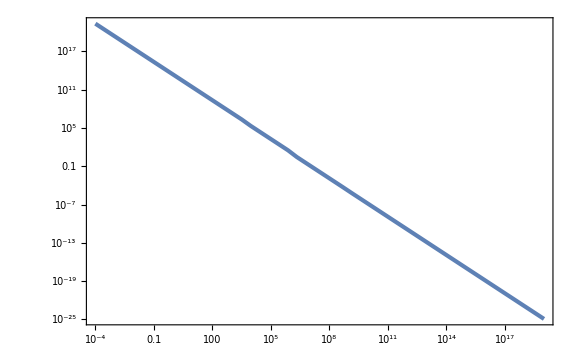

```mathematica
LogLogPlot[MH[k,gsT[Tk[k]]],{k,10^-4,10^19}]
```

```mathematica
MHticks=
Table[If[i==-20||i==-10||i==10||i==20,{k/.FindRoot[MH[k,gsT[Tk[k]]]==10^i,{k,10^6 10^(-i/2)}],10^ToString[i],0.01},If[i==0,{k/.FindRoot[MH[k,gsT[Tk[k]]]==1,{k,10^6}],1,0.01},{k/.FindRoot[MH[k,gsT[Tk[k]]]==10^i,{k,10^6 10^(-i/2)}],"",0.005}]],{i,-24,20,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{3.48827×10^18,,0.005},{3.48827×10^17,,0.005},{3.48827×10^16,10^-20,0.01},{3.48827×10^15,,0.005},{3.48827×10^14,,0.005},{3.48827×10^13,,0.005},{3.48827×10^12,,0.005},{3.48827×10^11,10^-10,0.01},{3.48827×10^10,,0.005},{3.48827×10^9,,0.005},{3.55081×10^8,,0.005},{3.55081×10^7,,0.005},{3.55081×10^6,1,0.01},{422367.,,0.005},{42236.7,,0.005},{4651.19,,0.005},{465.119,,0.005},{46.5119,10^10,0.01},{4.65119,,0.005},{0.465119,,0.005},{0.0465119,,0.005},{0.00465119,,0.005},{0.000465119,10^20,0.01}}

```mathematica
Map[MH[#[[1]],gsT[Tk[#[[1]]]]]&,MHticks]
```

{1.×10^-24,1.×10^-22,1.×10^-20,1.×10^-18,1.×10^-16,1.×10^-14,1.×10^-12,1.×10^-10,1.×10^-8,1.×10^-6,0.0001,0.01,1.,100.,10000.,1.×10^6,1.×10^8,1.×10^10,1.×10^12,1.×10^14,1.×10^16,1.×10^18,1.×10^20}

```mathematica
PLticks=Sort[Join[ Table[{10^i,10^ToString[i],0.01},{i,-10,-2,2}],Table[{10^i,"",0.005},{i,-9,-1,2}],{{1,1}}]];
PRticks=Sort[Join[ Table[{10^i,"",0.01},{i,-10,0,2}],Table[{10^i,"",0.005},{i,-9,-1,2}]]];
kticks=Table[If[i==5||i==10||i==15,{10^i,10^ToString[i],0.01},If[i==0,{1,1,0.01},{10^i,"",0.005}]],{i,-4,19}];
```

```mathematica
Pflat[k_]=((Tanh[(Log[ks]-Log[k])/σ2]+1)/2(k/ks)^4+(Tanh[(Log[k]-Log[ks])/σ2]+1)/2(k/ks)^(-0.01Log[k/ks]))As/.{ks->10^8,As->10^-2,σ2->0.4};
Pmulti[k_]=((Tanh[(Log[k1]-Log[k])/σ2]+1)/2(k/k1)^3+(Tanh[(Log[k]-Log[k1])/σ2]+1)/2(k/k1)^(3-2Sqrt[9/4+5])+(Tanh[(Log[k2]-Log[k])/σ2]+1)/2(k/k2)^3+(Tanh[(Log[k]-Log[k2])/σ2]+1)/2(k/k2)^(3-2Sqrt[9/4+5])+(Tanh[(Log[k3]-Log[k])/σ2]+1)/2(k/k3)^3+(Tanh[(Log[k]-Log[k3])/σ2]+1)/2(k/k3)^(3-2Sqrt[9/4+5]))As/.{k1->10^6,k2->10^10,k3->10^14,As->10^-2,σ2->0.2};
Phybrid[k_]=As Exp[(-Log[k/ks]^2)/(2σ2)]/.{ks->10^12,As->10^-2,σ2->2};
Pcurv[k_]=As (k/ks)^2(Tanh[Log[ks/k]/σ2]+1)/2/.{ks->10^12,As->10^-2,σ2->10^-3};
```

```mathematica
PgeoList=Select[Table[If[(etamax^2 Exp[-NN^2/σ2]/.{σ2->10,etamax->22})>=2,
k=ks Exp[NN]Sqrt[Abs[1-etamax^2 Exp[-NN^2/σ2]]/Abs[1-etamax^2]]/.{σ2->10,etamax->22,ks->10^12},k=ks Exp[NN]/Sqrt[Abs[1-etamax^2]]/.{σ2->10,etamax->22,ks->10^12}];
{k,2.1 10^-9(k/0.05)^(0.965-1) Exp[π(2-Sqrt[3])etamax Exp[-NN^2/(2σ2)]]/.{σ2->10,etamax->20}},{NN,-20,20,10^-2}],#[[1]]>10^5&];
Clear[k]
```

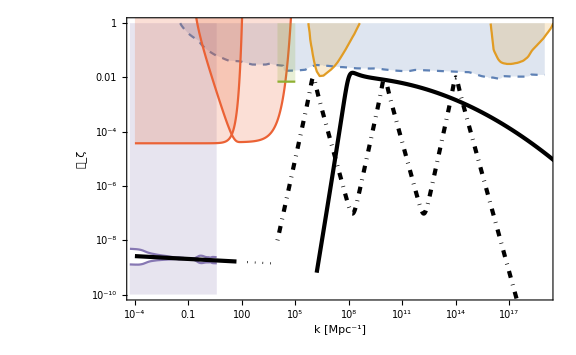

```mathematica
Show[ListLogLogPlot[{PBHconst,CMBLSSlow,CMBLSShigh,EPTA,(*LIGOO2*)LIGOO3},PlotRange->{{10^-4,10^19},{10^-10,1}},PlotStyle->{Dashed,Color[5],Color[5],Color[2],Color[2]},Filling->{1->Top,2->Bottom,3->Top,4->Top,5->Top},FrameTicks->{{PLticks,PRticks},{kticks,MHticks}},FrameLabel->{{Subscript[𝒫, ζ],None},{"k [Mpc^-1]","M / M_☉"}}],LogLogPlot[CMBmu[k],{k,10^-1,10^5},PlotStyle->Color[4],Filling->Top],LogLogPlot[CMBy[k],{k,10^-4,10^5},PlotStyle->Color[4],Filling->Top],LogLogPlot[0.007,{k,10^4,10^5},PlotStyle->Color[3],Filling->Top],LogLogPlot[2.1 10^-9(k/0.05)^(0.965-1),{k,10^-4,5 10},PlotStyle->{Black,AbsoluteThickness[3]}],LogLogPlot[2.1 10^-9(k/0.05)^(0.965-1),{k,2 10^2,10^4},PlotStyle->{Black,Dotted}],LogLogPlot[Pflat[k],{k,10^6.2,10^20},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[3]}],LogLogPlot[Pmulti[k],{k,10^4,10^20},PlotRange->Full,PlotStyle->{Black,AbsoluteThickness[3],DotDashed}](*,LogLogPlot[Phybrid[k],{k,10^7.5,10^20},PlotRange->Full,PlotStyle->{Color[3],Thick,Dashed}],ListLogLogPlot[PgeoList ,PlotRange->Full,PlotStyle->{Color[5],Thick,Dashed}],LogLogPlot[Pcurv[k],{k,10^5,10^20},PlotRange->Full,PlotStyle->{Color[6],Thick,Dashed}]*)]
```

## const on power

### DM

```mathematica
gsdata=Import["gs_dof.dat"];
```

```mathematica
gList=Map[{#[[1]],#[[2]]}&,gsdata];
gint[T_]=Interpolation[gList][T];
```

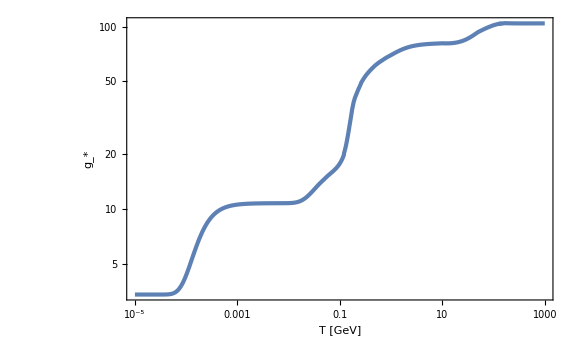

```mathematica
LogLogPlot[gint[T],{T,10^-5,10^3},FrameLabel->{"T [GeV]",SubStar[g]}]
```

```mathematica
KinGeV=10^-9/(1.160 10^4);
Omh2=0.143;
aeq=1/(2.4 10^4 Omh2);
keq=0.07Omh2;
Teq=(2.725KinGeV)/aeq
geq=3.38;
kinT[T_]=keq 2(Sqrt[2]-1)(gint[T]/geq)^(1/6)T/Teq;
```

8.06224×10^-10

```mathematica
kinT[10^-9]
```

0.0102872

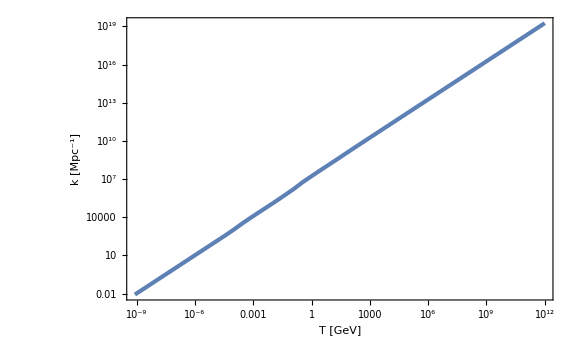

```mathematica
LogLogPlot[kinT[T],{T,Teq,10^12},FrameLabel->{"T [GeV]","k [Mpc^-1]"}]
```

```mathematica
T20=T/.FindRoot[kinT[T]==1.56 10^13,{T,10^5}]
```

856114.

```mathematica
muinM[MoMk_]=FullSimplify[mu/.Solve[MoMk==xm^2 E^(2mu Sin[xm]/xm)(mu-muth)^γ,mu][[1]],{γ>0,xm>0}]/.{muth->0.615,xm->2.74,γ->0.36}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.615+1.26175 ProductLog[0.00180051 MoMk^2.77778]

```mathematica
f[xi_]=1/2 xi(xi^2-3)(Erf[1/2 Sqrt[5/2]xi]+Erf[Sqrt[5/2]xi])+Sqrt[2/(5π)]((8/5+31/4 xi^2)Exp[-5/8 xi^2]+(-8/5+1/2 xi^2)Exp[-5/2 xi^2]);
PG[x_,A_]=1/Sqrt[2π A] Exp[-x^2/(2A)];
```

```mathematica
dlnMdmu[mu_]=0.282+0.36/(mu-0.615);
```

```mathematica
fPBH[MoMk_,A_,T_]=MoMk (gint[T]/106.75)^(-1/6)kinT[T]/(1.56 10^13)(dlnMdmu[muinM[MoMk]]^-1 f[muinM[MoMk]/Sqrt[A]]PG[muinM[MoMk],A])/(5.3 10^-16);
```

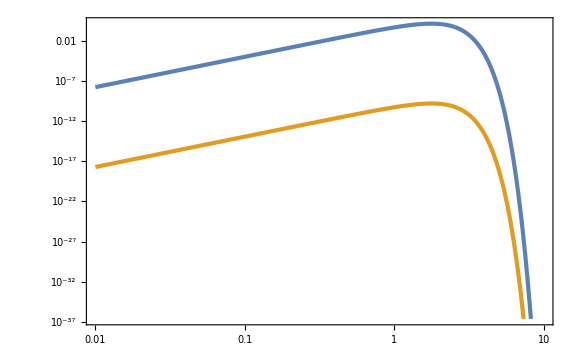

```mathematica
LogLogPlot[{fPBH[MoMk,4.863 10^-3,T20],fPBH[MoMk,4.863 10^-3,10^-4]},{MoMk,10^-2,10}]
```

```mathematica
NIntegrate[fPBH[MoMk,4.863 10^-3,T20]/MoMk,{MoMk,10^-2,5}]
```

1.05463

```mathematica
fM[MoMk_,A_]=(dlnMdmu[muinM[MoMk]]^-1 f[muinM[MoMk]/Sqrt[A]]PG[muinM[MoMk],A])/(5.3 10^-16);
```

```mathematica
NIntegrate[fM[MoMk,10^0],{MoMk,10^-2,5}]
```

1.49965×10^12

```mathematica
fMintegList=Table[{10^lnA,NIntegrate[fM[MoMk,10^lnA],{MoMk,10^-2,5}]},{lnA,-3,0,1/100}];
```

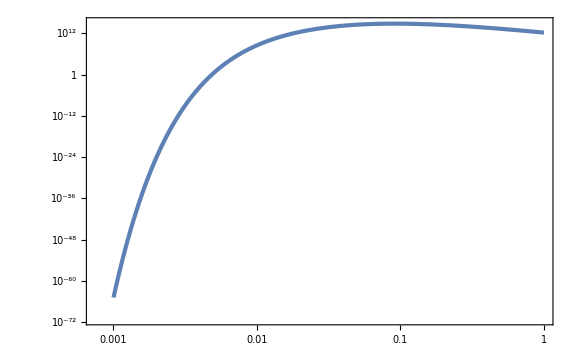

```mathematica
ListLogLogPlot[fMintegList]
```

```mathematica
fMint[A_]=Interpolation[fMintegList][A];
```

```mathematica
fMmax=FindMaximum[fMint[A],{A,0.09}][[1]]
Amax=A/.FindMaximum[fMint[A],{A,0.09}][[2]]
```

6.08364×10^14

0.0911834

```mathematica
Tmin=T/.FindRoot[(gint[T]/106.75)^(-1/6)kinT[T]/(1.56 10^13)fMmax==1,{T,10^-8}]
```

1.40223×10^-9

```mathematica
FindRoot[(gint[Tmin]/106.75)^(-1/6)kinT[Tmin]/(1.56 10^13)fMint[A]==1,{A,10^-2,10^-3,Amax}]
```

FindRoot::reged: The point {0.0911834} is at the edge of the search region {0.001,0.0911834} in coordinate 1 and the computed search direction points outside the region.

{A→0.0911834}

```mathematica
AconstDM=Table[{kinT[10^lnT],A/.FindRoot[(gint[10^lnT]/106.75)^(-1/6)kinT[10^lnT]/(1.56 10^13)fMint[A]==1,{A,10^-2,10^-3,Amax}]},{lnT,Log10[Tmin],12,1/100}];
```

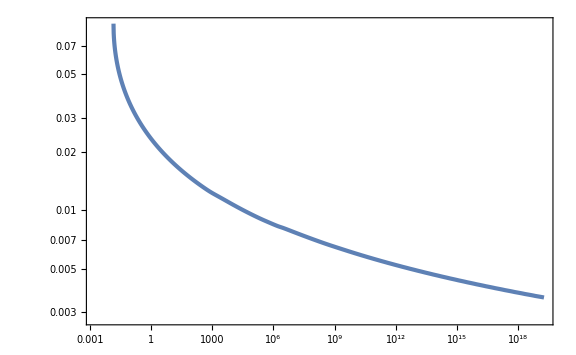

```mathematica
ListLogLogPlot[AconstDM]
```

```mathematica
Msol=1.988 10^33;
```

```mathematica
MinT[T_]=10^20(gint[T]/106.75)^(-1/6)(kinT[T]/(1.56 10^13))^-2;
```

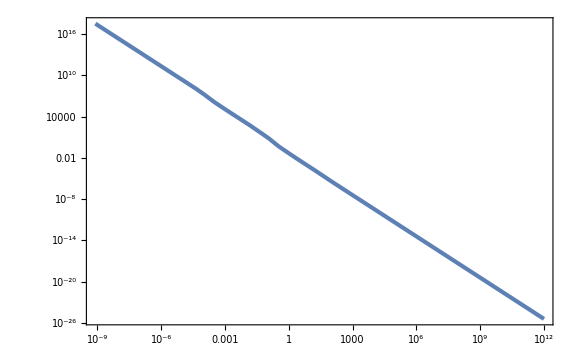

```mathematica
LogLogPlot[MinT[T]/Msol,{T,Teq,10^12}]
```

```mathematica
Export["AconstDM.dat",AconstDM];
```

### EGB

```mathematica
Ms=5 10^14;
fEGB[M_]=2 10^-8(M/Ms)^3.2;
MminEGB=2Ms;
MmaxEGB=(2 10^-8)^(-1/3.2)Ms
TminEGB=T/.FindRoot[10^-2 MinT[T]==MmaxEGB,{T,1}]
TmaxEGB=T/.FindRoot[5MinT[T]==MminEGB,{T,1}]
```

1.2732×10^17

2.40329×10^6

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

6.0604×10^8

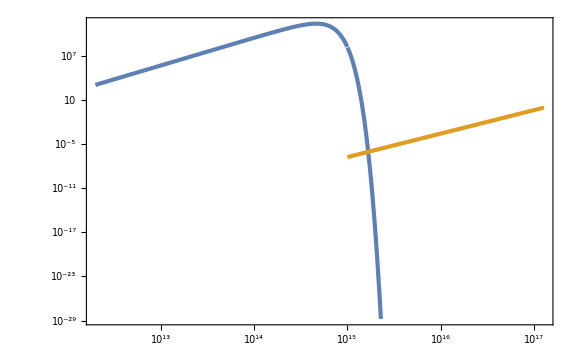

```mathematica
LogLogPlot[{fPBH[M/MinT[TmaxEGB],10^-2,TmaxEGB],fEGB[M]UnitStep[M-MminEGB]},{M,10^-2 MinT[TmaxEGB],MmaxEGB}]
```

```mathematica
Ts=TmaxEGB E^(-1/1000);
NIntegrate[fPBH[M/MinT[Ts],10^-2,Ts]/(fEGB[M]M),{M,Max[10^-2 MinT[Ts],MminEGB],Min[5MinT[Ts],MmaxEGB]}]
```

1.91343×10^12

```mathematica
ftotEGBList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fEGB[M]M),{M,Max[10^-2 MinT[10^lnT],MminEGB],Min[5MinT[10^lnT],MmaxEGB]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminEGB],Log10[TmaxEGB],1/100},{lnA,-3,-2,1/100}],1];//AbsoluteTiming
```

{28.4194,Null}

```mathematica
ftotEGBint[k_,A_]=Interpolation[ftotEGBList,InterpolationOrder->1][k,A]
```

InterpolatingFunction[…][k,A]

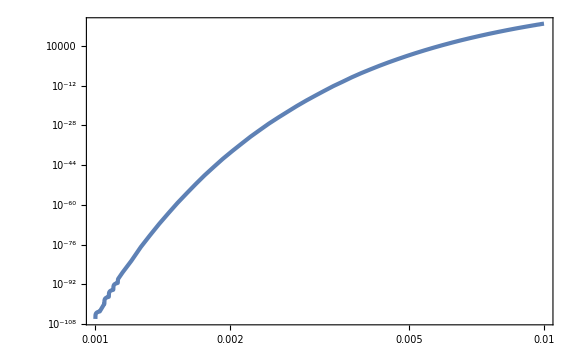

```mathematica
LogLogPlot[ftotEGBint[1.1005055258039372*^16,A],{A,10^-3,10^-2}]
```

```mathematica
FindRoot[ftotEGBint[kinT[TminEGB],A]==1,{A,5 10^-3}]
```

InterpolatingFunction::dmval: Input value {4.37959×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.37959×10^13,5.03} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.37959×10^13,2.5175} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{A→0.005}

```mathematica
AconstEGB=Table[{10^lnk,A/.FindRoot[ftotEGBint[10^lnk,A]==1,{A,5 10^-3}]},{lnk,Log10[kinT[TminEGB]]+1/100,Log10[kinT[TmaxEGB]],1/100}];
```

InterpolatingFunction::dmval: Input value {4.4816×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4816×10^13,1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.4816×10^13,0.5075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

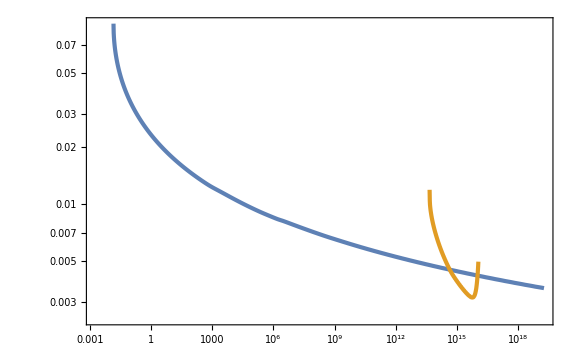

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB}]
```

```mathematica
Export["AconstEGB.dat",AconstEGB];
```

### GC

```mathematica
GCdata=Import["GC.csv"];
```

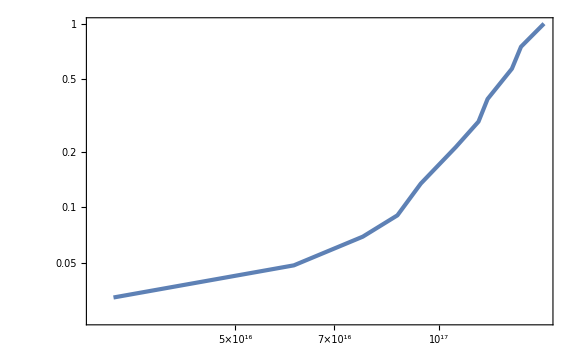

```mathematica
ListLogLogPlot[GCdata]
```

```mathematica
fGC[M_]=Interpolation[GCdata,InterpolationOrder->1][M];
MminGC=First[GCdata][[1]];
MmaxGC=Last[GCdata][[1]];
TminGC=T/.FindRoot[10^-2 MinT[T]==MmaxGC,{T,1}]
TmaxGC=T/.FindRoot[5MinT[T]==MminGC,{T,1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

2.26609×10^6

1.0548×10^8

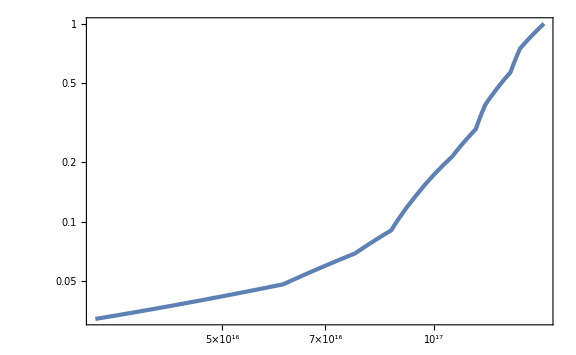

```mathematica
LogLogPlot[fGC[M],{M,MminGC,MmaxGC}]
```

```mathematica
ftotGCList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fGC[M]M),{M,Max[10^-2 MinT[10^lnT],MminGC],Min[5MinT[10^lnT],MmaxGC]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminGC],Log10[TmaxGC],1/100},{lnA,-3,-2,1/100}],1];//AbsoluteTiming
```

{105.232,Null}

```mathematica
ftotGCint[k_,A_]=Interpolation[ftotGCList,InterpolationOrder->1][k,A];
```

```mathematica
AconstGC=Table[{10^lnk,A/.FindRoot[ftotGCint[10^lnk,A]==1,{A,5 10^-3}]},{lnk,Log10[kinT[TminGC]]+1/100,Log10[kinT[TmaxGC]],1/100}];
```

InterpolatingFunction::dmval: Input value {4.22573×10^13,10.055} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.22573×10^13,1.01} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.22573×10^13,0.5075} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

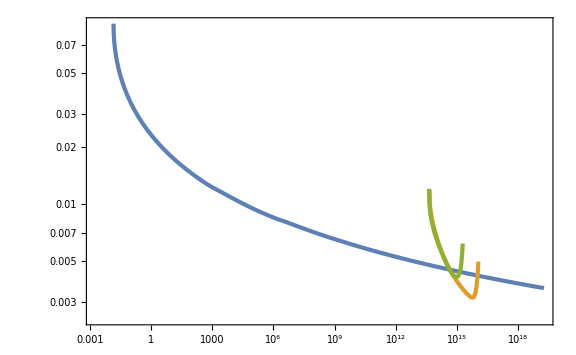

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC}]
```

```mathematica
AconstEGBint[k_]=Interpolation[AconstEGB][k];
AconstGCint[k_]=Interpolation[AconstGC][k];
```

```mathematica
AconstEvap[k_]=Min[AconstEGBint[k],AconstGCint[k]];
```

InterpolatingFunction::dmval: Input value {4.22621×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

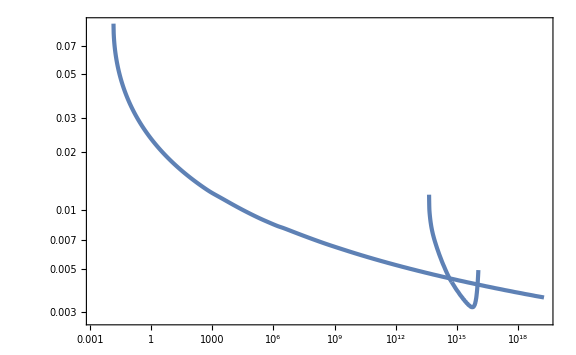

```mathematica
Show[ListLogLogPlot[AconstDM],LogLogPlot[AconstEvap[k],{k,First[AconstGC][[1]],Last[AconstEGB][[1]]}]]
```

```mathematica
Export["AconstGC.dat",AconstGC];
```

### lensing

```mathematica
Lensdata=Import["lensing.csv"];
```

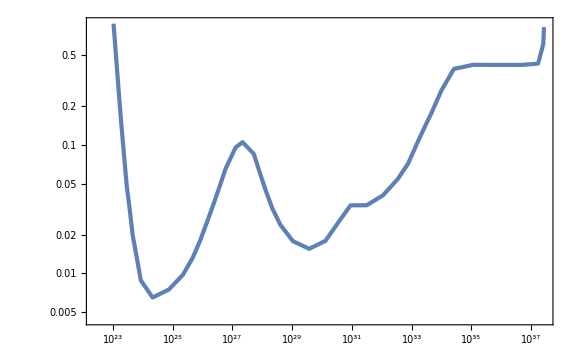

```mathematica
ListLogLogPlot[Lensdata]
```

```mathematica
fLens[M_]=Interpolation[Lensdata,InterpolationOrder->1][M];
MminLens=First[Lensdata][[1]]
MmaxLens=Last[Lensdata][[1]]
TminLens=T/.FindRoot[10^-2 MinT[T]==MmaxLens,{T,10^-4}]
TmaxLens=T/.FindRoot[5MinT[T]==MminLens,{T,1}]
```

1.04659×10^23

2.69574×10^37

0.000305436

59297.7

```mathematica
ftotLensList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fLens[M]M),{M,Max[10^-2 MinT[10^lnT],MminLens],Min[5MinT[10^lnT],MmaxLens]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminLens],Log10[TmaxLens],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{855.702,Null}

```mathematica
ftotLensint[k_,A_]=Interpolation[ftotLensList,InterpolationOrder->1][k,A];
```

```mathematica
kinT[TminLens]
kinT[TmaxLens]
```

3694.4

1.08029×10^12

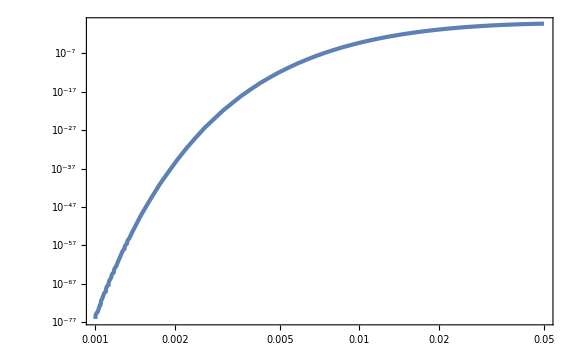

```mathematica
LogLogPlot[ftotLensint[1.5 10^4,A],{A,10^-3,5 10^-2}]
```

```mathematica
AconstLens=Select[Table[{10^lnk,If[ftotLensint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotLensint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminLens]]+1/100,Log10[kinT[TmaxLens]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {3780.45,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3868.51,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3958.62,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

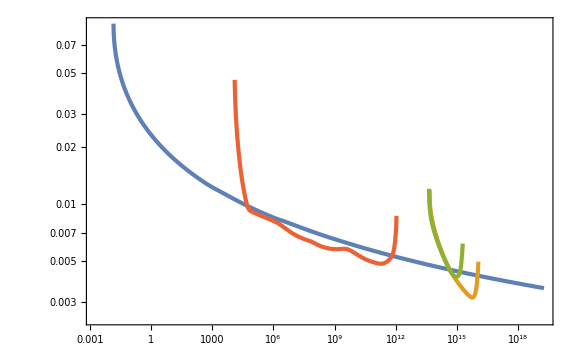

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens}]
```

```mathematica
Export["AconstLens.dat",AconstLens];
```

### XB

```mathematica
XBdata=Import["XB.csv"];
```

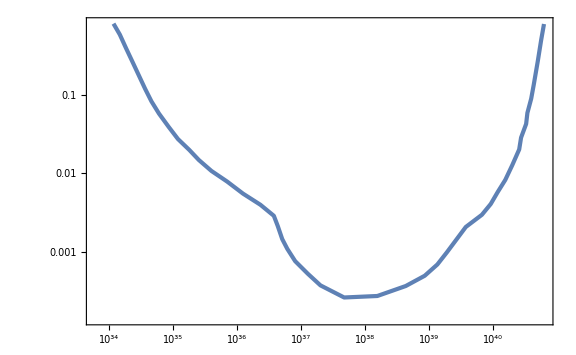

```mathematica
ListLogLogPlot[XBdata]
```

```mathematica
fXB[M_]=Interpolation[XBdata,InterpolationOrder->1][M];
MminXB=First[XBdata][[1]]
MmaxXB=Last[XBdata][[1]]
TminXB=T/.FindRoot[10^-2 MinT[T]==MmaxXB,{T,10^-4}]
TmaxXB=T/.FindRoot[5MinT[T]==MminXB,{T,1}]
```

1.17208×10^34

6.37908×10^40

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

8.00513×10^-6

0.219997

```mathematica
ftotXBList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fXB[M]M),{M,Max[10^-2 MinT[10^lnT],MminXB],Min[5MinT[10^lnT],MmaxXB]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminXB],Log10[TmaxXB],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{669.367,Null}

```mathematica
ftotXBint[k_,A_]=Interpolation[ftotXBList,InterpolationOrder->1][k,A];
```

```mathematica
AconstXB=Select[Table[{10^lnk,If[ftotXBint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotXBint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminXB]]+1/100,Log10[kinT[TmaxXB]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {84.2688,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {86.2317,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {88.2403,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

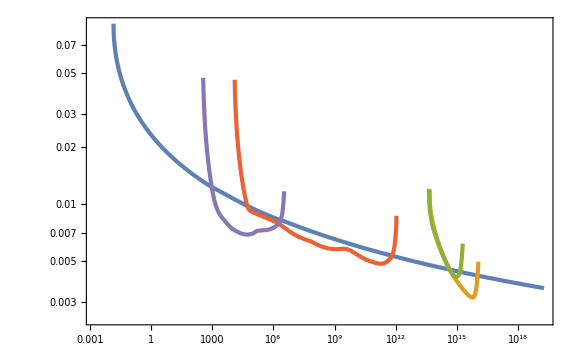

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB}]
```

```mathematica
Export["AconstXB.dat",AconstXB];
```

### DF

```mathematica
DFdata=Import["DF.csv"];
```

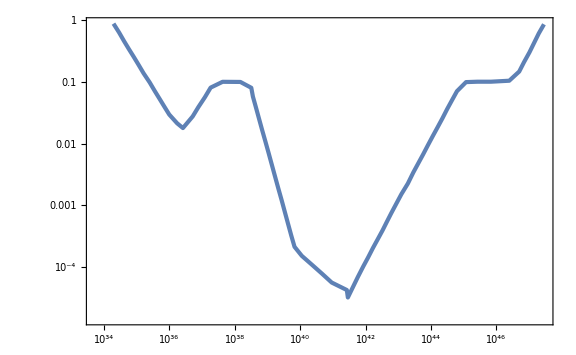

```mathematica
ListLogLogPlot[DFdata]
```

```mathematica
fDF[M_]=Interpolation[DFdata,InterpolationOrder->1][M];
MminDF=First[DFdata][[1]]
MmaxDF=Last[DFdata][[1]]
TminDF=T/.FindRoot[10^-2 MinT[T]==MmaxDF,{T,10^-10}]
TmaxDF=T/.FindRoot[5MinT[T]==MminDF,{T,1}]
```

1.95625×10^34

2.87185×10^47

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

3.77282×10^-9

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.178489

```mathematica
ftotDFList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fDF[M]M),{M,Max[10^-2 MinT[10^lnT],MminDF],Min[5MinT[10^lnT],MmaxDF]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminDF],Log10[TmaxDF],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{1124.93,Null}

```mathematica
ftotDFint[k_,A_]=Interpolation[ftotDFList,InterpolationOrder->1][k,A];
```

```mathematica
AconstDF=Select[Table[{10^lnk,If[ftotDFint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotDFint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminDF]]+1/100,Log10[kinT[TmaxDF]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {0.0397159,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.040641,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0415877,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

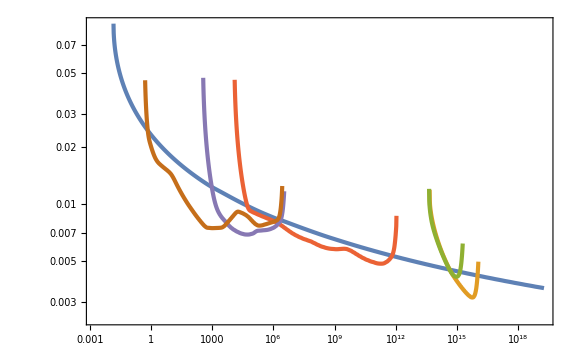

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB,AconstDF}]
```

```mathematica
Export["AconstDF.dat",AconstDF];
```

### LSS

```mathematica
LSSdata=Import["LSS.csv"];
```

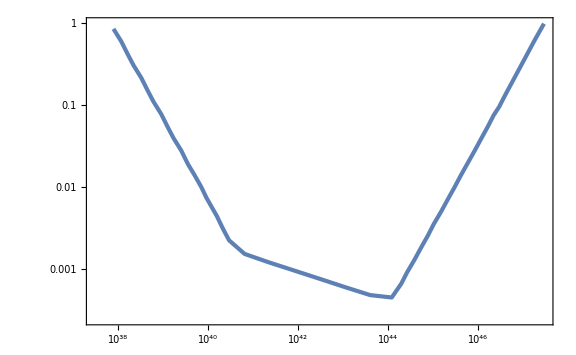

```mathematica
ListLogLogPlot[LSSdata]
```

```mathematica
fLSS[M_]=Interpolation[LSSdata,InterpolationOrder->1][M];
MminLSS=First[LSSdata][[1]]
MmaxLSS=Last[LSSdata][[1]]
TminLSS=T/.FindRoot[10^-2 MinT[T]==MmaxLSS,{T,10^-10}]
TmaxLSS=T/.FindRoot[5MinT[T]==MminLSS,{T,10^-5}]
```

7.94933×10^37

2.99961×10^47

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

3.6916×10^-9

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.00380034

```mathematica
ftotLSSList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fLSS[M]M),{M,Max[10^-2 MinT[10^lnT],MminLSS],Min[5MinT[10^lnT],MmaxLSS]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminLSS],Log10[TmaxLSS],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{722.43,Null}

```mathematica
ftotLSSint[k_,A_]=Interpolation[ftotLSSList,InterpolationOrder->1][k,A];
```

```mathematica
AconstLSS=Select[Table[{10^lnk,If[ftotLSSint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotLSSint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminLSS]]+1/100,Log10[kinT[TmaxLSS]],1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {0.038861,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0397662,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.0406924,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

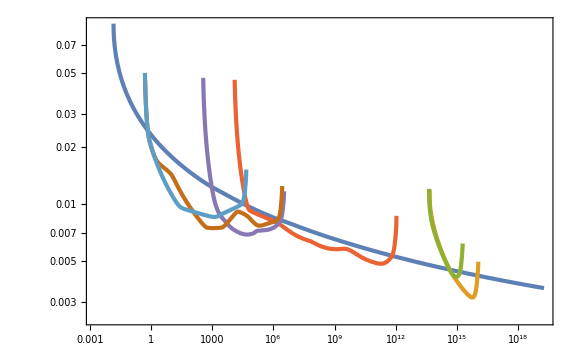

```mathematica
ListLogLogPlot[{AconstDM,AconstEGB,AconstGC,AconstLens,AconstXB,AconstDF,AconstLSS}]
```

```mathematica
Export["AconstLSS.dat",AconstLSS];
```

### GW

```mathematica
GWdata=Import["GW.csv"];
```

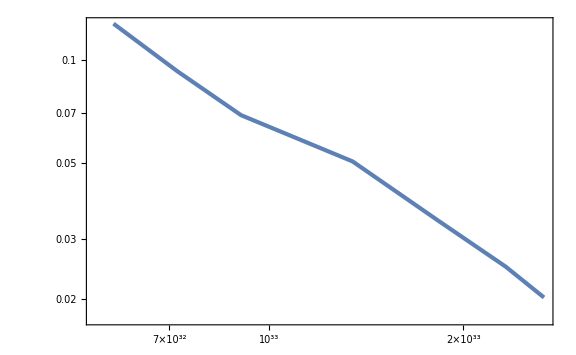

```mathematica
ListLogLogPlot[GWdata]
```

```mathematica
fGW[M_]=Interpolation[GWdata,InterpolationOrder->1][M];
MminGW=First[GWdata][[1]]
MmaxGW=Last[GWdata][[1]]
TminGW=T/.FindRoot[10^-2 MinT[T]==MmaxGW,{T,10^-2}]
TmaxGW=T/.FindRoot[5MinT[T]==MminGW,{T,1}]
```

5.73953×10^32

2.66856×10^33

0.028314

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.889347

```mathematica
ftotGWList=Flatten[ParallelTable[{kinT[10^lnT],10^lnA,NIntegrate[fPBH[M/MinT[10^lnT],10^lnA,10^lnT]/(fGW[M]M),{M,Max[10^-2 MinT[10^lnT],MminGW],Min[5MinT[10^lnT],MmaxGW]}(*,WorkingPrecision->30*)]//Quiet},{lnT,Log10[TminGW],Log10[TmaxGW],1/100},{lnA,-3,Log10[5/100],1/100}],1];//AbsoluteTiming
```

{92.5014,Null}

```mathematica
ftotGWint[k_,A_]=Interpolation[ftotGWList,InterpolationOrder->1][k,A];
```

```mathematica
AconstGW=Select[Table[{10^lnk,If[ftotGWint[10^lnk,5 10^-2]>1,A/.FindRoot[ftotGWint[10^lnk,A]==1,{A,10^-2}(*,WorkingPrecision->30*)],None]},{lnk,Log10[kinT[TminGW]]+1/100,Log10[kinT[TmaxGW]]-1/100,1/100}],#[[2]]>0&];
```

InterpolatingFunction::dmval: Input value {369861.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {378476.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {387292.,1/20} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
AconstDM=Import["AconstDM.dat"];
AconstEGB=Import["AconstEGB.dat"];
AconstGC=Import["AconstGC.dat"];
AconstLens=Import["AconstLens.dat"];
AconstXB=Import["AconstXB.dat"];
AconstDF=Import["AconstDF.dat"];
AconstLSS=Import["AconstLSS.dat"];
AconstGW=Import["AconstGW.dat"];
```

```mathematica
AconstEGBint[k_]=Interpolation[AconstEGB][k];
AconstGCint[k_]=Interpolation[AconstGC][k];
```

```mathematica
AconstEvap[k_]=Min[AconstEGBint[k],AconstGCint[k]];
```

```mathematica
EvapC=RGBColor["#FF0000"];
LensC=RGBColor["#0000FF"];
XBC=RGBColor["#00AAAA"];
DFC=RGBColor["#00AA00"];
LSSC=RGBColor["#FFB3FF"];
GWC=RGBColor["#AAAAAA"];
```

```mathematica
MHticks=
Table[If[i==-20||i==-10||i==10||i==20,{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,-i/2}],10^ToString[i],{0.01,0}},If[i==0,{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,0}],1,{0.01,0}},{kinT[10^logT]/.FindRoot[MinT[10^logT]==10^i Msol,{logT,-i/2}],"",{0.005,0}}]],{i,-24,20,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{3.50371×10^18,,{0.005,0}},{3.50391×10^17,,{0.005,0}},{3.50412×10^16,10^-20,{0.01,0}},{3.50436×10^15,,{0.005,0}},{3.50463×10^14,,{0.005,0}},{3.50491×10^13,,{0.005,0}},{3.50522×10^12,,{0.005,0}},{3.50553×10^11,10^-10,{0.01,0}},{3.50583×10^10,,{0.005,0}},{3.50545×10^9,,{0.005,0}},{3.57594×10^8,,{0.005,0}},{3.59617×10^7,,{0.005,0}},{3.75272×10^6,1,{0.01,0}},{417307.,,{0.005,0}},{42374.1,,{0.005,0}},{4286.77,,{0.005,0}},{466.374,,{0.005,0}},{46.6485,10^10,{0.01,0}},{4.66485,,{0.005,0}},{0.466485,,{0.005,0}},{0.0466485,,{0.005,0}},{0.00466485,,{0.005,0}},{0.000466485,10^20,{0.01,0}}}

InterpolatingFunction::dmval: Input value {4.22621×10^13} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

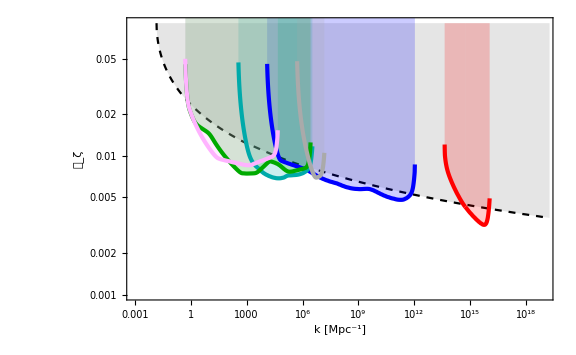

```mathematica
PconstPBH=Show[ListLogLogPlot[AconstDM,FrameLabel->{{Subscript[𝒫, ζ],None},{"k [Mpc^-1]",Row[{Subscript[M, H][k]," / ",M_☉}]}},PlotStyle->{Black,Dashed},Filling->Top,PlotRange->{{10^-3,10^19},{0.001,0.09}},FillingStyle->Directive[Opacity[0.1]],FrameTicks->{Automatic,{Automatic,MHticks}}],ListLogLogPlot[{AconstLens,AconstXB,AconstDF,AconstLSS,AconstGW},Filling->Top,PlotRange->{0.001,0.9},PlotStyle->{{AbsoluteThickness[3],LensC},{AbsoluteThickness[3],XBC},{AbsoluteThickness[3],DFC},{AbsoluteThickness[3],LSSC},{AbsoluteThickness[3],GWC}}],LogLogPlot[AconstEvap[k],{k,First[AconstGC][[1]],Last[AconstEGB][[1]]},Filling->Top,PlotRange->{0.001,0.09},PlotStyle->{AbsoluteThickness[3],EvapC}]]
```

```mathematica
Export["AconstGW.dat",AconstGW];
```